```mathematica
(*ver. 1.0 by Grzegorz Rajchel-Mieldzioć on 2021-04-13, summarizing work from arXiv:2104.05122 
author list:
Suhail Ahmad Rather
  Adam Burchardt
  Wojciech Bruzda
  Grzegorz Rajchel-Mieldzioć
  Arul Lakshminarayan
  Karol Życzkowski*)
(*In order to use this file, first compile the whole preamble*)
```

## Preamble with functions

First, the most important functions, i.e. reshuffle and partial transpose, taken from qi package https://zksi.iitis.pl/wiki/projects:mathematica-qi

```mathematica
Reshuffle[ρ_]:=Block[{dim},
	dim = Sqrt[Length[ρ]];
	If[And [SquareMatrixQ[ρ] , IntegerQ[dim]] ,
		Reshuffle[ρ, {{dim,dim},{dim,dim}}]
	(*else*),
		Message[Reshuffle::argerr]
	]
]
Reshuffle::argerr = "Reshuffle works only for square matrices of dimension \!\(\*SuperscriptBox[\"d\", \"2\"]\)×\!\(\*SuperscriptBox[\"d\", \"2\"]\), \
where d is an Integer, for other dimensions use ReshuffleGeneral";
Reshuffle[A_,{n_,m_}]:=Flatten[
	Table[Flatten[Part[A,1+i1;;n[[2]]+i1,1+i2;;m[[2]]+i2]],{i1,0,n[[1]] n[[2]]-1,n[[2]]},{i2,0,m[[1]]*m[[2]]-1,m[[2]]}]
,1];
PartialTranspose[a_]:=Module[{dim,sdim,temp},
dim=Dimensions[a][[1]];
sdim=Sqrt[dim];
temp=Partition[a,{sdim,sdim}];
temp=Map[Transpose,temp,{2}];
temp=ArrayFlatten[temp];
Return[temp];
];
```

We create swap matrix, which is permutation matrix defined that state {i,j}<->{j,i}.

```mathematica
swapFunction[i_,dim_]:=dim Mod[i-1,dim]+1+Floor[(i-1)/dim];
swap[dim_]:=Table[If[swapFunction[i,dim]==j,1,0],{i,dim^2},{j,dim^2}];
```

Measures of the linear entropy, entangling power and gate typicality of a state, following Clarisse et al., Phys. Rev. A 72, 012314.
These are normalized so that Max[linEntropy] = 1, Max[entPower] = 1, Max[gt] = 1.

```mathematica
linEntropy[A_]:=(Length@A)/(Length@A-1)(1-Tr[((A.A†)/Tr[A.A†]).((A.A†)/Tr[A.A†])]);
entPower[A_]:=Chop@N@((Length@A)/(Length@A+1))(linEntropy@Reshuffle[A]+linEntropy@Reshuffle[A.swap[√(Length@A)]]-linEntropy@swap[√(Length@A)]);
gt[A_]:=Chop@N@(1/2)(linEntropy@Reshuffle[A]-linEntropy@Reshuffle[A.swap[√(Length@A)]]+linEntropy@swap[√(Length@A)]);
```

## Main body with state

```mathematica
AME46=({{0, 1/(√2), 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(-(3 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^((2 ⅈ π)/5))/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -ⅇ^((4 ⅈ π)/5)/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)) ⅇ^((4 ⅈ π)/5), 0, 0, 0, 0, -1/2 ⅈ √(1/5 (5+√5)) ⅇ^((4 ⅈ π)/5), -ⅇ^((4 ⅈ π)/5)/(√(5+√5))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((3 ⅈ π)/10)/(√(5+√5)), 1/2 √(1/5 (5+√5)), 0, 0, 0, 0, 1/2 √(1/5 (5+√5)), ⅇ^((7 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 √(1/5 (5+√5)), ⅈ/(√(5+√5)), 0, 0, 0, 0, ⅈ/(√(5+√5)), 1/2 √(1/5 (5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)) ⅇ^((9 ⅈ π)/10), ⅇ^((ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, -ⅈ/(√(5+√5)), -1/2 √(1/5 (5+√5)) ⅇ^((ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((7 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, (ⅈ ⅇ^(-(3 ⅈ π)/5))/(√2), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^((7 ⅈ π)/10))/(√(5+√5)), 1/2 √(1/5 (5+√5)) ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)) ⅇ^((4 ⅈ π)/5), 1/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, (ⅈ ⅇ^((ⅈ π)/10))/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^((ⅈ π)/5)/(√(5+√5)), 1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(2 ⅈ π)/5), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)), -(ⅈ ⅇ^(-(ⅈ π)/10))/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/2 √(1/5 (5+√5)) ⅇ^((2 ⅈ π)/5), -(ⅈ ⅇ^((4 ⅈ π)/5))/(√(5+√5)), 0, 0, 0, 0, (ⅈ ⅇ^((2 ⅈ π)/5))/(√(5+√5)), -1/2 √(1/5 (5+√5)) ⅇ^((4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((4 ⅈ π)/5)/(√2), 0, 0, 0, 0, 0, 0, (ⅈ ⅇ^(-(9 ⅈ π)/10))/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^((7 ⅈ π)/10))/(√2), 0, 0, 0, 0, -(ⅈ ⅇ^((7 ⅈ π)/10))/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅈ/(√2), 0, 0, 0, 0, -ⅇ^((9 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), -1/2 √(1/5 (5+√5)), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(ⅈ π)/10), (ⅈ ⅇ^(-(ⅈ π)/5))/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(7 ⅈ π)/10)/(√2), 0, 0, 0, 0, 0, 0, ⅇ^((7 ⅈ π)/10)/(√2), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(4 ⅈ π)/5)/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)), 0, 0, 0, 0, 1/2 √(1/5 (5+√5)) ⅇ^((ⅈ π)/10), (ⅈ ⅇ^((9 ⅈ π)/10))/(√(5+√5)), 0, 0}, {0, 0, 0, 0, ⅇ^((ⅈ π)/10)/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(ⅈ π)/10), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(9 ⅈ π)/10), ⅇ^(-(ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2 √(1/5 (5+√5)), ⅈ/(√(5+√5)), 0, 0, 0, 0, -ⅈ/(√(5+√5)), 1/2 √(1/5 (5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 √(1/5 (5+√5)) ⅇ^(-(3 ⅈ π)/5), ⅇ^((7 ⅈ π)/10)/(√(5+√5)), 0, 0, 0, 0, ⅇ^(-(7 ⅈ π)/10)/(√(5+√5)), 1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(9 ⅈ π)/10), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/2 √(1/5 (5+√5)), ⅈ/(√(5+√5)), 0, 0, 0, 0, ⅈ/(√(5+√5)), -1/2 √(1/5 (5+√5))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^((2 ⅈ π)/5)/(√(5+√5)), 1/2 √(1/5 (5+√5)) ⅇ^(-(3 ⅈ π)/10), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)) ⅇ^((ⅈ π)/5), -1/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)), 0, 0, 0, 0, -1/2 ⅈ √(1/5 (5+√5)), 1/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(-(3 ⅈ π)/5)/(√2), 0, 0, 0, 0, -1/(√2), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, -1/(√2), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 √(1/5 (5+√5)) ⅇ^((7 ⅈ π)/10), -1/(√(5+√5)), 0, 0, 0, 0, 1/(√(5+√5)), 1/2 ⅈ √(1/5 (5+√5)) ⅇ^((4 ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1/2 ⅈ √(1/5 (5+√5)) ⅇ^((7 ⅈ π)/10), ⅈ/(√(5+√5)), 0, 0, 0, 0, -ⅈ/(√(5+√5)), -1/2 √(1/5 (5+√5)) ⅇ^(-(ⅈ π)/5), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(√2), 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^((ⅈ π)/10))/(√2), 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)), 0, 0, 0, 0, 1/2 ⅈ √(1/5 (5+√5)), 1/(√(5+√5)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(ⅈ π)/10), (ⅈ ⅇ^(-(ⅈ π)/5))/(√(5+√5)), 0, 0, 0, 0, ⅇ^((7 ⅈ π)/10)/(√(5+√5)), -1/2 ⅈ √(1/5 (5+√5)) ⅇ^(-(9 ⅈ π)/10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^((3 ⅈ π)/5))/(√2), 0, 0, 0, 0, 0, 0, -(ⅈ ⅇ^(-(2 ⅈ π)/5))/(√2)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2 √(1/5 (5+√5)) ⅇ^((9 ⅈ π)/10), ⅇ^(-(2 ⅈ π)/5)/(√(5+√5)), 0, 0, 0, 0, -ⅇ^((3 ⅈ π)/5)/(√(5+√5)), 1/2 √(1/5 (5+√5)) ⅇ^(-(7 ⅈ π)/10), 0, 0, 0, 0}});
```

```mathematica
(*Below reshuffled and partially transposed version of the AME(4,6) state*)
AME46//Reshuffle;
AME46//PartialTranspose;
```

Below matrices with absolute values depicted

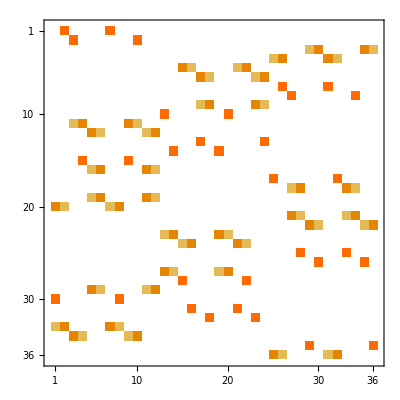
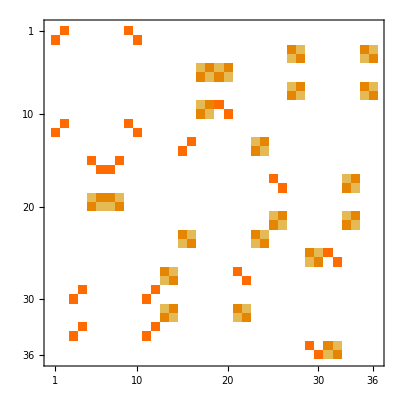
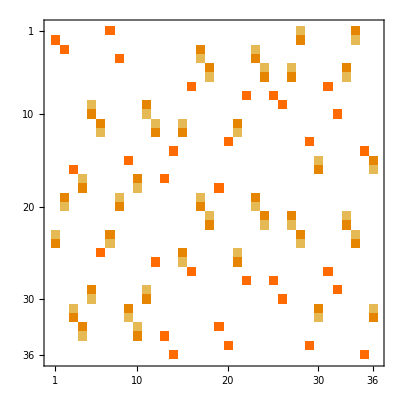

```mathematica
Row[MatrixPlot[#,ImageSize->400]&/@Abs/@{AME46,Reshuffle@AME46,PartialTranspose@AME46}]
```

#### Proof that this is AME(4,6)

In order to show that our matrix defines an AME state we only need to check the unitarity of the reshuffling, partial transposition and the matrix itself.
Below we present UU†, which equals identity in all of these three cases.

```mathematica
MatrixForm@FullSimplify[#.#†]&/@{AME46,Reshuffle@AME46,PartialTranspose@AME46}
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

#### Permutations which bring it to the block-diagonal form

Below we list the permutations which correspond to the diagonalization of AME(4,6)

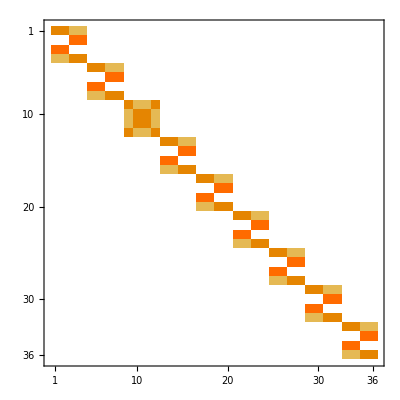

```mathematica
{rowPerm,colPerm}={{20,1,30,33,34,15,2,11,12,16,19,29,27,14,10,23,5,31,28,24,6,32,13,9,36,7,17,4,21,25,8,18,22,26,35,3},{1,8,7,2,3,10,9,4,5,6,11,12,13,20,19,14,15,22,21,16,17,24,23,18,25,32,31,26,27,34,33,28,29,36,35,30}};
AME46⟦rowPerm,colPerm⟧//Abs//MatrixPlot
```

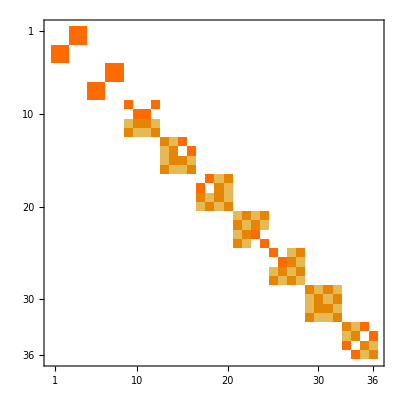

```mathematica
{rowPerm,colPerm}={{1,11,2,12,29,33,30,34,15,16,19,20,27,28,31,32,13,14,23,24,5,6,9,10,17,18,21,22,3,4,7,8,25,26,35,36},{1,10,2,9,3,11,4,12,5,6,7,8,13,14,21,22,15,16,23,24,17,18,19,20,25,26,33,34,27,28,35,36,29,30,31,32}};
(Reshuffle@AME46)⟦rowPerm,colPerm⟧//Abs//MatrixPlot
```

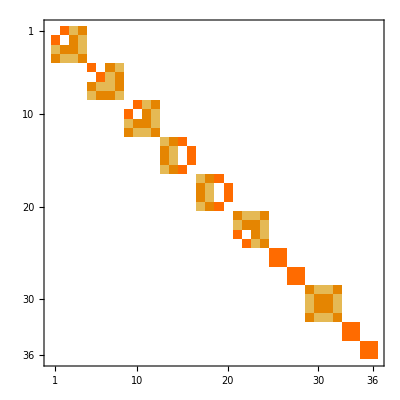

```mathematica
{rowPerm,colPerm}={{1,2,23,24,3,4,19,20,15,16,31,32,17,18,33,34,9,10,29,30,11,12,25,26,14,36,7,27,5,6,21,22,13,35,8,28},{1,7,28,34,2,8,17,23,3,9,30,36,4,10,13,19,5,11,26,32,6,12,15,21,14,35,16,31,18,24,27,33,20,29,22,25}};
(PartialTranspose@AME46)⟦rowPerm,colPerm⟧//Abs//MatrixPlot
```

#### Card form of AME(4,6)

Similarly to the description from our paper, we can present the state as an array of cards

```mathematica
toBase6[n_]:=({a,b}={Floor[(n-1)/6],Mod[n-1,6]};
If[b==0,b=♠];
If[b==1,b=♣];
If[b==2,b=♢];
If[b==3,b=♡];
If[b==4,b=⌘];
If[b==5,b=✶];
If[a==0,a="A"];
If[a==1,a="K"];
If[a==2,a="Q"];
If[a==3,a="J"];
If[a==4,a="10"];
If[a==5,a="9"];
a<>ToString[b]
);
(toBase6/@Range@36)
```

{A♠,A♣,A♢,A♡,A⌘,A✶,K♠,K♣,K♢,K♡,K⌘,K✶,Q♠,Q♣,Q♢,Q♡,Q⌘,Q✶,J♠,J♣,J♢,J♡,J⌘,J✶,10♠,10♣,10♢,10♡,10⌘,10✶,9♠,9♣,9♢,9♡,9⌘,9✶}

```mathematica
(*nonzero elements of AME(4,6) indexed by increasing row number, so that they fill 6x6 array*)
nonZero=DeleteDuplicates[DeleteCases[#,_Integer]]&/@Abs@AME46;
nonZero=Module[{n},Table[(n=6(i-1)+j;nonZero⟦n⟧),{i,6},{j,6}]];
Module[{n,tempTable,tempList,iter},Table[(n=6(i-1)+j;tempTable={};tempList={};For[iter=1,iter≤Length@nonZero⟦i,j⟧,iter++,
AppendTo[tempList,nonZero⟦i,j,iter⟧];
tempList=Reverse@Sort[tempList];];
For[iter=1,iter≤Length@tempList,iter++,AppendTo[tempTable,Flatten@{Flatten[toBase6/@Flatten@Position[Abs@AME46⟦n⟧,tempList⟦iter⟧]],NumberForm[N@Abs@tempList⟦iter⟧,3]}];];
tempTable),{i,6},{j,6}]//MatrixForm]
```

({{A♣,K♠,0.707}} | {{A♢,K♡,0.707}} | {{10⌘,9✶,0.372},{10✶,9⌘,0.602}} | {{10♠,9♣,0.372},{10♣,9♠,0.602}} | {{Q♡,J♢,0.372},{Q♢,J♡,0.602}} | {{Q✶,J⌘,0.372},{Q⌘,J✶,0.602}}
{{10♣,9♠,0.707}} | {{10♢,9♡,0.707}} | {{Q⌘,J✶,0.372},{Q✶,J⌘,0.602}} | {{Q♠,J♣,0.707}} | {{A♢,K♡,0.372},{A♡,K♢,0.602}} | {{A✶,K⌘,0.372},{A⌘,K✶,0.602}}
{{Q⌘,J✶,0.707}} | {{Q♣,J♠,0.707}} | {{A♡,K♢,0.707}} | {{A⌘,K✶,0.372},{A✶,K⌘,0.602}} | {{10♠,9♣,0.707}} | {{10♢,9♡,0.372},{10♡,9♢,0.602}}
{{A⌘,K✶,0.372},{A✶,K⌘,0.602}} | {{A♣,K♠,0.372},{A♠,K♣,0.602}} | {{10♡,9♢,0.372},{10♢,9♡,0.602}} | {{10✶,9⌘,0.372},{10⌘,9✶,0.602}} | {{Q♠,J♣,0.372},{Q♣,J♠,0.602}} | {{Q♢,J♡,0.372},{Q♡,J♢,0.602}}
{{10♡,9♢,0.707}} | {{10✶,9⌘,0.707}} | {{Q♣,J♠,0.372},{Q♠,J♣,0.602}} | {{Q♢,J♡,0.707}} | {{A✶,K⌘,0.372},{A⌘,K✶,0.602}} | {{A♠,K♣,0.707}}
{{Q♡,J♢,0.707}} | {{Q✶,J⌘,0.707}} | {{A♠,K♣,0.372},{A♣,K♠,0.602}} | {{A♡,K♢,0.372},{A♢,K♡,0.602}} | {{10⌘,9✶,0.707}} | {{10♣,9♠,0.372},{10♠,9♣,0.602}})

This is precisely the same form of the AME state as in the Fig. 2 of the “36 entangled officers of Euler” paper.

#### Quantum AME state

Below we present the state which follows from the 2-unitary matrix in the LATEX form. 
Code below requires MaTeX package to present this in the graphical form, otherwise it just produces .tex code.

```mathematica
<<MaTeX`;
(*remove zeros from the matrix and keep the column of each non-zero element*)
posNon[x_]:=Module[{list,iter,full={},index,iter2},
list=DeleteDuplicates@Select[x,#≠0&];
For[iter=1,iter≤Length@list,iter++,
index=Flatten@Position[x,list⟦iter⟧];
For[iter2=1,iter2≤Length@index,iter2++,
AppendTo[full,{index⟦iter2⟧,list⟦iter⟧}];
];
];
full
];
(*to each element add its row number*)
row2number[A_]:=Module[{iter1,iter2,tempMat=A},For[iter1=1,iter1≤Length@A,iter1++,
For[iter2=1,iter2≤Length@A⟦iter1⟧,iter2++,
tempMat⟦iter1,iter2⟧=Join[{iter1},A⟦iter1,iter2⟧];
];
];
tempMat
];
(*change a number from {1,...,36} to 2 numbers from {1,...,6}*)
index6[n_]:={Floor[(n-1)/6]+1,Mod[n-1,6]+1};
(*'addPlus' adds plus to the output if there's no minus so that there is a proper formatting after latexing*)
addPlus[A_]:=Module[{temp=A⟦2⟧},If[StringTake[ToString[TeXForm@temp],{1}]=="-",temp=ToString[TeXForm@temp];,temp="+"<>ToString[TeXForm@temp];];
{A⟦1⟧,temp}
];
(*elem2ket changes elements of matrix into quantum kets*)
elem2ket[A_]:=A⟦2⟧<>"|"<>ToString[A⟦1,1⟧]<>ToString[A⟦1,2⟧]<>ToString[A⟦1,3⟧]<>ToString[A⟦1,4⟧]<>"\\rangle";
(*final function which can present any matrix in the LaTeX quantum state format*)
teXState[A_]:=StringJoin[elem2ket/@Map[addPlus,{Flatten[{index6@#⟦1⟧,index6@#⟦2⟧}],#⟦3⟧}&/@Flatten[row2number[posNon[#]&/@A],1]]];

MaTeX@teXState[AME46]
teXState[AME46]
```

-Graphics-

+\frac{1}{\sqrt{2}}|1112\rangle+\frac{1}{\sqrt{2}}|1121\rangle+\frac{e^{-\frac{3 i \pi }{10}}}{\sqrt{2}}|1213\rangle-\frac{i e^{\frac{2 i \pi }{5}}}{\sqrt{2}}|1224\rangle-\frac{e^{\frac{4 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|1355\rangle-\frac{e^{\frac{4 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|1366\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{4 i \pi }{5}}|1356\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{4 i \pi }{5}}|1365\rangle+\frac{e^{\frac{3 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|1451\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|1452\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|1461\rangle+\frac{e^{\frac{7 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|1462\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|1533\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|1544\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|1534\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|1543\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{9 i \pi }{10}}|1635\rangle+\frac{e^{\frac{i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|1636\rangle-\frac{i}{\sqrt{5+\sqrt{5}}}|1645\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{i \pi }{5}}|1646\rangle+\frac{1}{\sqrt{2}}|2152\rangle+\frac{1}{\sqrt{2}}|2161\rangle+\frac{1}{\sqrt{2}}|2112\rangle-\frac{1}{\sqrt{2}}|2161\rangle+\frac{e^{\frac{7 i \pi }{10}}}{\sqrt{2}}|2253\rangle+\frac{i e^{-\frac{3 i \pi }{5}}}{\sqrt{2}}|2264\rangle-\frac{i e^{\frac{7 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|2335\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{i \pi }{10}}|2336\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{4 i \pi }{5}}|2345\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|2335\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|2312\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|2346\rangle-\frac{1}{\sqrt{2}}|2431\rangle+\frac{i e^{\frac{i \pi }{10}}}{\sqrt{2}}|2442\rangle+\frac{e^{\frac{i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|2513\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{2 i \pi }{5}}|2514\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|2523\rangle-\frac{i e^{-\frac{i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|2524\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{2 i \pi }{5}}|2615\rangle-\frac{i e^{\frac{4 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|2616\rangle+\frac{i e^{\frac{2 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|2625\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{4 i \pi }{5}}|2626\rangle+\frac{e^{\frac{4 i \pi }{5}}}{\sqrt{2}}|3135\rangle+\frac{i e^{-\frac{9 i \pi }{10}}}{\sqrt{2}}|3146\rangle-\frac{i e^{\frac{7 i \pi }{10}}}{\sqrt{2}}|3232\rangle-\frac{i e^{\frac{7 i \pi }{10}}}{\sqrt{2}}|3241\rangle+\frac{i}{\sqrt{2}}|3314\rangle-\frac{e^{\frac{9 i \pi }{10}}}{\sqrt{2}}|3323\rangle+\frac{e^{\frac{i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|3415\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|3416\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{i \pi }{10}}|3425\rangle+\frac{i e^{-\frac{i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|3426\rangle+\frac{e^{-\frac{7 i \pi }{10}}}{\sqrt{2}}|3551\rangle+\frac{e^{\frac{7 i \pi }{10}}}{\sqrt{2}}|3562\rangle+\frac{e^{-\frac{4 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|3653\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|3654\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{i \pi }{10}}|3663\rangle+\frac{i e^{\frac{9 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|3664\rangle+\frac{e^{\frac{i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|4115\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{i \pi }{10}}|4116\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{9 i \pi }{10}}|4125\rangle+\frac{e^{-\frac{i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|4126\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4211\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|4212\rangle-\frac{i}{\sqrt{5+\sqrt{5}}}|4221\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4222\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{3 i \pi }{5}}|4353\rangle+\frac{e^{\frac{7 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|4354\rangle+\frac{e^{-\frac{7 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|4363\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{9 i \pi }{10}}|4364\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4455\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4466\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|4456\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|4465\rangle+\frac{e^{\frac{2 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|4531\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{3 i \pi }{10}}|4532\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{i \pi }{5}}|4541\rangle-\frac{1}{\sqrt{5+\sqrt{5}}}|4542\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|4633\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|4644\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4634\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|4643\rangle+\frac{e^{-\frac{3 i \pi }{5}}}{\sqrt{2}}|5154\rangle-\frac{1}{\sqrt{2}}|5163\rangle+\frac{1}{\sqrt{2}}|5256\rangle+\frac{1}{\sqrt{2}}|5265\rangle+\frac{1}{\sqrt{2}}|5212\rangle-\frac{1}{\sqrt{2}}|5265\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{7 i \pi }{10}}|5331\rangle-\frac{1}{\sqrt{5+\sqrt{5}}}|5332\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|5332\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|5312\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|5341\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{4 i \pi }{5}}|5342\rangle+\frac{1}{\sqrt{2}}|5433\rangle+\frac{1}{\sqrt{2}}|5444\rangle+\frac{1}{\sqrt{2}}|5412\rangle-\frac{1}{\sqrt{2}}|5444\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{7 i \pi }{10}}|5515\rangle+\frac{i}{\sqrt{5+\sqrt{5}}}|5516\rangle-\frac{i}{\sqrt{5+\sqrt{5}}}|5525\rangle-\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{i \pi }{5}}|5526\rangle+\frac{1}{\sqrt{2}}|5611\rangle+\frac{1}{\sqrt{2}}|5622\rangle+\frac{1}{\sqrt{2}}|6134\rangle+\frac{1}{\sqrt{2}}|6143\rangle+\frac{1}{\sqrt{2}}|6112\rangle-\frac{1}{\sqrt{2}}|6143\rangle-\frac{i e^{\frac{i \pi }{10}}}{\sqrt{2}}|6236\rangle+\frac{1}{\sqrt{2}}|6236\rangle+\frac{1}{\sqrt{2}}|6212\rangle+\frac{1}{\sqrt{2}}|6245\rangle-\frac{1}{\sqrt{5+\sqrt{5}}}|6311\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|6312\rangle+\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)}|6321\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|6311\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|6312\rangle+\frac{1}{\sqrt{5+\sqrt{5}}}|6322\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{i \pi }{10}}|6413\rangle+\frac{i e^{-\frac{i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|6414\rangle+\frac{e^{\frac{7 i \pi }{10}}}{\sqrt{5+\sqrt{5}}}|6423\rangle-\frac{1}{2} i \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{9 i \pi }{10}}|6424\rangle-\frac{i e^{\frac{3 i \pi }{5}}}{\sqrt{2}}|6555\rangle-\frac{i e^{-\frac{2 i \pi }{5}}}{\sqrt{2}}|6566\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{\frac{9 i \pi }{10}}|6651\rangle+\frac{e^{-\frac{2 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|6652\rangle-\frac{e^{\frac{3 i \pi }{5}}}{\sqrt{5+\sqrt{5}}}|6661\rangle+\frac{1}{2} \sqrt{\frac{1}{5} \left(5+\sqrt{5}\right)} e^{-\frac{7 i \pi }{10}}|6662\rangle

## Additional matrices and the history of finding

#### Best permutation matrix as of Clarisse et al., known even earlier

```mathematica
bestPerm=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

#### Improved matrices by Arul Lakshminarayan and Wojciech Bruzda from X and XII 2017

```mathematica
arulMatrix=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, (√3)/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, (√3)/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, 1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/2, (√3)/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, 1/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/2, (√3)/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
bruzdaMatrix=Module[{θ1=π/6,θ2=-π/6},({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Cos[θ1], 0, 0, 0, 0, 0, 0, Sin[θ1], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Sin[θ1], 0, 0, 0, 0, 0, 0, Cos[θ1], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Cos[θ2], 0, 0, 0, 0, 0, 0, Sin[θ2], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Sin[θ2], 0, 0, 0, 0, 0, 0, Cos[θ2], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})];
```

#### Extension beyond the line by Wojciech Bruzda and Grzegorz Rajchel-Mieldzioc from X 2018

```mathematica
bruzdaMatrix2=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, 1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, -1/(√2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1/2, 0, 0, 0, 0, 0, 0, (√3)/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, 0, 0, 0, 0, 0, 0, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -(-1+√3)/(2 √2), 0, 0, 0, 0, -(1+√3)/(2 √2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (1+√3)/(2 √2), 0, 0, 0, 0, -(-1+√3)/(2 √2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(-1+√3)/(2 √2), 0, 0, 0, 0, -(1+√3)/(2 √2), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(1+√3)/(2 √2), 0, 0, 0, 0, (-1+√3)/(2 √2), 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(√3)/2, 0, 0, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/2, 0, 0, 0, 0, 0, 0, -(√3)/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
matrixRotated[α_,β_,γ_]:=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Cos[α], 0, 0, 0, 0, 0, 0, Sin[α], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -Sin[α], 0, 0, 0, 0, 0, 0, Cos[α], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Cos[β], 0, 0, 0, 0, 0, 0, Sin[β], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Sin[β], 0, 0, 0, 0, 0, 0, -Cos[β], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Cos[γ], 0, 0, 0, 0, 0, 0, -Sin[γ], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Sin[γ], 0, 0, 0, 0, 0, 0, Cos[γ], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

Matrix, which has the highest entPower, which is at the corner of the elipse, has the following form:

```mathematica
rajchelMatrix=matrixRotated[1/4π,3/8π,1/8π];
```

#### Original numerical AME by Suhail Ahmad Rather from VII 2020

```mathematica
suhAME=({{0.4899151664852252619`18.69012088427954+0.4453773467653378004`18.648728123733033 ⅈ, -0.1029692340494765823`18.012707482195776-0.2397698260724511476`18.379794528242567 ⅈ, -0.02863513506481470822`18.456899235913305+0.001320994425000471262`18.12090098476317 ⅈ, 0.1237991725169969442`18.09271774183674-0.1890050833351721582`18.276473484780265 ⅈ, 0.05615289387209521782`18.749372142793327-0.01785119130526240105`18.251667204203823 ⅈ, 0.09223111088502163046`18.96487743956404-0.2392106976898012438`18.378780597740132 ⅈ, -0.09114822520154064467`18.95974821668072+0.02661066844587373081`18.42505578393539 ⅈ, -0.1788030679827657676`18.252374966342195+0.1683743982595142796`18.226276056641723 ⅈ, -0.1554321351562185649`18.191540812909086+0.01114109235359879088`18.04692777431011 ⅈ, -0.1646929729043342394`18.216675069151677+0.2716248162654198994`18.433969445559818 ⅈ, -0.3185736441820664622`18.503209843468387+0.1264577575721462788`18.101945476364772 ⅈ, 0.194613083726809355`18.289172034284576+0.05001278566963576061`18.69908104505473 ⅈ, 0.00002514780728805746291`18.40050012361811+0.004449634551381059788`18.648324343826783 ⅈ, -0.01677190530364110199`18.22458240165532-0.007992537367056806036`18.90268467538084 ⅈ, -0.007131448300202687662`18.85317773811446-0.02390141006990020855`18.37842352301979 ⅈ, -0.03655048962659557255`18.562893199097008-0.0001551082405580536672`18.190634871532634 ⅈ, -0.008827080137617321354`18.945817069395428+0.009334881401572313331`18.97010880466647 ⅈ, 0.02831785597875439292`18.45206036865599+0.01149993290866540598`18.06069530665958 ⅈ, 0.01792667537043285408`18.253499754026496-0.01393372435813565804`18.144067214916458 ⅈ, 0.007502632112368477768`18.87521365157006+0.04025156458266859749`18.604782766105462 ⅈ, -0.01451988313766083838`18.161963120987128+0.02795089738365206383`18.4463957557828 ⅈ, -0.01239886422728148779`18.09338190432226+0.03524903988864061533`18.547147292199927 ⅈ, 0.0395372042380627009`18.59700595615343+0.04207828296904312509`18.624058009846163 ⅈ, 0.02806976097585169028`18.448238714475885+0.008798188640673311467`18.944393269385017 ⅈ, 0.02363160503279218561`18.373493219440782-0.05087923112795210423`18.706540539758862 ⅈ, 0.002797838306948390724`18.446822612075326+0.01614647365828575376`18.208077688402728 ⅈ, -0.003408337934981381379`18.532542648307594+0.002644735302241046915`18.422382212277217 ⅈ, -0.008250543442721284051`18.91648255538654+0.002994891739272073639`18.47638112793183 ⅈ, 0.02214636691761567855`18.34530249096338+0.01895721374074128482`18.277774506739306 ⅈ, -0.004244324532166172947`18.627808583792078+0.0157516694295812415`18.19732658895947 ⅈ, -0.004378301382694878632`18.641305653151587+0.002576503035419022702`18.411030658446602 ⅈ, 0.01960493790308749651`18.29236547104892-0.006806964318572132633`18.83295347408222 ⅈ, 0.006982137543828370596`18.843988399897427+0.01270330115367624899`18.103916593910927 ⅈ, -0.00248899992560457084`18.39602488362767-0.02173664088053482366`18.337192430285466 ⅈ, 0.0233456295999689839`18.36820559075795-0.01663091460086380674`18.220916133476052 ⅈ, -0.02375237124655766446`18.375706972608846+0.02681208347854337204`18.42833056288543 ⅈ}, {-0.1080451228089641114`18.033605167471364-0.1049242081681357325`18.02087570040431 ⅈ, -0.2438651625006987289`18.38714976335456+0.1105120843108374218`18.04340976999005 ⅈ, 0.1359241496599511156`18.133296624740545-0.01435087447446128581`18.156878365729376 ⅈ, 0.1797881640418682037`18.254761097516784-0.06879410812524444641`18.837551244656066 ⅈ, -0.2127628206469498462`18.3278957392312-0.3557383465043608139`18.551130682103487 ⅈ, -0.04563989613117405697`18.65934464736517-0.1819385132306252373`18.25992464141151 ⅈ, 0.01557149836317100328`18.192330404446597+0.1442518791875560258`18.15912147947401 ⅈ, -0.2179103679385854808`18.338277893997503+0.0666316976950281914`18.823680878706977 ⅈ, 0.5882137780737415333`18.76953519302266-0.1300575838428431608`18.114135681599702 ⅈ, 0.02723907986446301444`18.43519243303019-0.1455523075204147587`18.163019094937585 ⅈ, -0.167884007352089748`18.225009327171147-0.0188770860293489065`18.275934955054975 ⅈ, 0.3139500282668215014`18.49686052649653+0.1889381952156726219`18.2763197625518 ⅈ, -0.002225392070754408924`18.34740653628989-0.01612018991506792079`18.207370154006306 ⅈ, 0.002106595487456869309`18.323581149546765+0.001167334662221564817`18.067195381426824 ⅈ, 0.003233260846445637493`18.50964074315229-0.01851826747564240538`18.267600352704193 ⅈ, 0.01658460482418216281`18.21970512766607-0.01800165935264286948`18.255312539241167 ⅈ, -0.009282434406885940736`18.96766188902363+0.02169683869180134492`18.336396460174683 ⅈ, -0.02630286578304427691`18.420003068868418+0.04463142345840253461`18.649640738291822 ⅈ, 0.007074026150023858539`18.84966666090566-0.008125211144316754966`18.90983465551186 ⅈ, -0.003966534502067162876`18.59841123625795+0.00839593276314601171`18.924068951979017 ⅈ, -0.03593850960234185044`18.55556006261992-0.07361756771980118574`18.86698146451898 ⅈ, -0.02713095798174434276`18.433465128772287-0.01506059957727920451`18.177842261899244 ⅈ, -0.02909372842633136877`18.463799380622213+0.01396253163412891976`18.14496417008156 ⅈ, 0.01712548517188199754`18.23364288407608-0.03706782980408404593`18.568997160302548 ⅈ, 0.004244748221376611064`18.627851935025276-0.002805370507260887547`18.44799022695858 ⅈ, -0.03555655302069360424`18.550919652279838-0.003273681279198175937`18.515036394861077 ⅈ, -0.02326314041936097116`18.366668342152416+0.005126514042941662797`18.709822151364428 ⅈ, 0.009353706715152287909`18.970983748511568-0.02674145682465442833`18.427185063123208 ⅈ, -0.03006518846299313652`18.47806393055576+0.01549517508099756968`18.190196487724805 ⅈ, -0.00730672024121125762`18.863722479450853+0.01002709224434868845`18.001175010256784 ⅈ, 0.01181599248056833251`18.07247020592875+0.02010787110986671233`18.303366092765852 ⅈ, 0.001731910570294814544`18.238525462837096-0.01644445889281406781`18.216019587534014 ⅈ, 0.007049717505616615032`18.84817171440843+0.01476491134005371991`18.16923084346899 ⅈ, -0.003181245363935096548`18.50259716677903-0.03449394692432083964`18.537742890783193 ⅈ, 0.000761431864809418435`18.88163104744726+0.02259373799323923654`18.353988088181982 ⅈ, -0.0130333960191774921`18.115057591478056-0.01711474720326038382`18.233370488689214 ⅈ}, {0.01110532689444920784`18.04553134688863-0.0188294452023892965`18.274837523994865 ⅈ, -0.0002650052514844569718`18.423254480231616-0.0009625752059448690334`18.983434670908757 ⅈ, -0.01852622145361943265`18.267786851095586+0.003401847242884212252`18.531714808082565 ⅈ, 0.008825781186265410638`18.94575315597142-0.0107680118149909021`18.032135523401312 ⅈ, -0.02315309611503934412`18.364609074652844+0.01793443874905539803`18.253687790155997 ⅈ, 0.02295290523553276257`18.36083766363826+0.01944149288948648913`18.288729610835745 ⅈ, -0.00387643108286657434`18.588432067269334-0.001475605750010641759`18.168970338878587 ⅈ, -0.003955534430800787538`18.597205169165566+0.002227987009160773552`18.34791265424575 ⅈ, -0.06875668428287594336`18.837314925135853-0.01554341319696517232`18.19154639218961 ⅈ, -0.02011075832398564328`18.303428447012116-0.007128126769004747287`18.852975414736687 ⅈ, -0.02226434020746705447`18.347609829559225+0.03939397993510679319`18.5954298593707 ⅈ, 0.02485251523050117928`18.395370348620627-0.03739304235592356279`18.572790801464397 ⅈ, 0.2097800046072883229`18.32176409061368+0.04004036189123207079`18.602497994048417 ⅈ, 0.5380796594550015799`18.730846575110206+0.1778773723841536314`18.250120705398604 ⅈ, 0.2298492832819401532`18.36144315386756+0.0008719551273983459916`18.94049413582165 ⅈ, -0.04188363078078255475`18.622044322474608+0.08875286384511592297`18.948182375609548 ⅈ, -0.2685246870503859573`18.428984219111552-0.04935921068865298245`18.693368206205427 ⅈ, -0.3321390489967063209`18.521319937829187+0.214118951129032703`18.330655107306253 ⅈ, 0.1698422987654629734`18.230045859245553+0.03667698815522077438`18.56439366502217 ⅈ, 0.1135846053909759373`18.055319473568606+0.1423784817172941974`18.153444357435674 ⅈ, -0.03038104412203587387`18.48260269542033-0.3657707936200401133`18.563209024606643 ⅈ, 0.1847158708895619839`18.26650421186494-0.2017461465420867794`18.304805248219434 ⅈ, 0.01907060060680759728`18.280364370870593-0.1400098891447364435`18.14615871174475 ⅈ, 0.05419230612596144525`18.733937632585917+0.1535795889454965035`18.18633350086891 ⅈ, 0.01934352670260416907`18.286535657329665+0.001003880326211896434`18.001681943124144 ⅈ, 0.02207504912166478872`18.34390167864799+0.02179343597194402515`18.338325706887673 ⅈ, -0.02556264882039091871`18.407605853730352+0.004749460187349757723`18.676644251524323 ⅈ, -0.01715849018364182244`18.23447907058957-0.02289970166235576199`18.359829824381958 ⅈ, 0.01608961471645089028`18.206545644563747-0.03087976870492353462`18.48967403873133 ⅈ, -0.009160139193117556103`18.96190207305034+0.006808254056095183748`18.833035753466305 ⅈ, -0.01555610066359055382`18.19190074480587-0.0002642341184718732805`18.42198889392723 ⅈ, 0.01059893695062382249`18.02526230869592-0.0356264179144574894`18.551772158073984 ⅈ, -0.02848476693293781892`18.454612670338143+0.01963174622105818071`18.292958931308643 ⅈ, -0.01319303142576385215`18.120344596927495-0.02017742184125088933`18.30486567371217 ⅈ, 0.01763502865828106558`18.246376169766098-0.002483823070506296568`18.395120656625526 ⅈ, 0.01118413932381175091`18.0486025685577+0.01814669722967925808`18.258797593259278 ⅈ}, {-0.04943472563687980464`18.694032128161023+0.03124584563071958546`18.494792282813176 ⅈ, 0.01592965834091667615`18.20220646115921-0.001462634024132256072`18.165135671864807 ⅈ, -0.01886818980746607019`18.27573023644798+0.01368805452232951803`18.13634172642052 ⅈ, 0.02208886468657844659`18.344173394774785+0.002351228414697537072`18.371294821563954 ⅈ, -0.01416953070434209296`18.151355466627862-0.01981967416600851489`18.29709651043848 ⅈ, -0.0007545241763546040037`18.877673159935576-0.002598211089966981358`18.414674432142593 ⅈ, -0.006105450495140329892`18.785717714199883+0.00802453996759175392`18.90442014447092 ⅈ, -0.01144004943529029067`18.058427901155206-0.02337285745144045829`18.368711810361077 ⅈ, 0.02821839254728859131`18.45053227066121-0.04977545776712700987`18.697015262769224 ⅈ, -0.04518443844473010035`18.654988889208916-0.007460741937831148578`18.87278201828819 ⅈ, -0.02523966376624298125`18.40208356509516-0.04130125763348593132`18.615963276231884 ⅈ, -0.02093377539653917818`18.320847560207845-0.04159864854745672774`18.619079221542226 ⅈ, 0.09948286294136166052`18.997748275007073+0.2511017127244246638`18.399849674975886 ⅈ, -0.0618921822349922518`18.79163579560132-0.1353128165246399728`18.131338933939187 ⅈ, -0.2371415383892498119`18.37500763290348-0.0157218107457644321`18.19650256407016 ⅈ, 0.001039667163781121673`18.016894327694438+0.3597260487187592948`18.555971887374287 ⅈ, 0.01161195486944298708`18.064905339251442-0.08651785836147976583`18.937105760497715 ⅈ, 0.00730096895800459722`18.863380501927164-0.1818430455769202425`18.25969669650802 ⅈ, -0.06090814221899801262`18.784675353132315-0.1825133222382080422`18.261294570509612 ⅈ, 0.3533052783350904003`18.548150125786616+0.1307840623741319819`18.11655482315726 ⅈ, 0.1790249908046530614`18.25291366009158+0.07127291141898335625`18.85292449960478 ⅈ, 0.1474500448566880562`18.168644909007245-0.1531933362073852889`18.18523987423063 ⅈ, 0.2201255266355137963`18.34267040799691-0.2612406353858764962`18.417040731375064 ⅈ, 0.4322996681890891035`18.635784902191755-0.2919806876524963513`18.465354127053477 ⅈ, 0.009494754489810353082`18.977483739468077+0.009028703563496637274`18.955625394207097 ⅈ, 0.02010717054021764899`18.303350961435868+0.003046164168591464216`18.48375330530078 ⅈ, -0.01976507182186788836`18.295898396811257-0.009900193567933826544`18.995643685977726 ⅈ, 0.0154905307267524904`18.19006629753658-0.005547042573372608365`18.744061499087753 ⅈ, 0.03531988129437034496`18.548019235299456-0.007309042332528600111`18.863860477239065 ⅈ, 0.01563020137128309783`18.193964573276624+0.0482354285596182375`18.683366141474373 ⅈ, 0.0007690654311453687386`18.88596329061616-0.005906962359620071545`18.771364203452773 ⅈ, -0.0380590821694233028`18.580458310657228+0.009329223320943502012`18.96984548924823 ⅈ, -0.01982472673640817834`18.297207209725432+0.04067270511828974949`18.609303058042087 ⅈ, 0.02658956228555355017`18.424711188082476-0.03800534389937264973`18.57984466669147 ⅈ, -0.01977366184641879757`18.296087102921668+0.01547653869386714232`18.189673837856024 ⅈ, -0.02311766442892650847`18.363943955316568+0.005456485828672195601`18.736913031611422 ⅈ}, {0.01055504666506657842`18.023460157713416-0.01824970526467836404`18.261255854931814 ⅈ, 0.002582223924792882708`18.411993900627987+0.001320705414330977656`18.120805958267272 ⅈ, -0.01746692604096647394`18.24221648134751-0.005080818980763832093`18.705933722157724 ⅈ, -0.04659183507376292444`18.668309815979757-0.01546479368628134177`18.189344130513966 ⅈ, -0.01640783936425036643`18.21505139555868-0.00784417747994626581`18.89454741132024 ⅈ, 0.01064484586021949286`18.027139377137352+0.02689386773091276273`18.42965326460344 ⅈ, -0.003858178410487286825`18.586382306485323-9.290687607177048821`18.968047857476076*^-6 ⅈ, 0.01203784381613932225`18.08054870431284+0.008077911474871635189`18.907299089464644 ⅈ, -0.009028038209070754147`18.955593388459942+0.03212585504823638888`18.50685469549232 ⅈ, 0.01763657561662035009`18.24641426474276+0.002324754799621291113`18.36637715301645 ⅈ, 0.01674151203235476129`18.22379467932351+0.01196869476802767118`18.07804679151327 ⅈ, -0.01435816086724145402`18.157098814811533+0.005216912436760728911`18.71741354737011 ⅈ, -0.03217491933026339623`18.50751746670415+0.008360257721212445078`18.922219665617874 ⅈ, -0.02944087782327121927`18.468950754990164-0.04818137869939470574`18.68287922307977 ⅈ, 0.01593675236615259977`18.20239982439009-0.007272024724713832544`18.861655346807492 ⅈ, -0.002534921967505699564`18.403964594989564-0.0130125164648780961`18.114361292036456 ⅈ, 0.02698548036243102188`18.431130153247864+0.00688522424157458901`18.837918089152502 ⅈ, 0.003613281818472896534`18.557901835754173+0.02499136748630548938`18.397790020652575 ⅈ, -0.0375028827661344627`18.574064652295867+0.009877785090710577975`18.994659573057174 ⅈ, -0.01151212510918775411`18.06115550069355-0.01150321428328101789`18.060819209957366 ⅈ, -0.03820649766063949349`18.582137228309396-0.006605878416868958547`18.819930576111556 ⅈ, -0.01342187164125331622`18.12781308116766+0.01333607271574453051`18.125027954843382 ⅈ, -0.02635879107226367368`18.42092548776246+0.0332430300606066792`18.521700602315036 ⅈ, -0.03087209608972599564`18.48956611731162-0.0006802240078358640085`18.83265195586286 ⅈ, 0.1592580196545735072`18.202101311048416+0.2330863928464519952`18.36751692095005 ⅈ, -0.04458807452454553732`18.649218718337043+0.1259001004500619469`18.100026076612156 ⅈ, -0.2321367120468432188`18.365743828859845-0.06747706897627622769`18.82915620973399 ⅈ, -0.03275750562639383884`18.515310824286903-0.4201155002218566192`18.62336870519102 ⅈ, 0.2822337356528379915`18.45060892413201-0.003171172470850379399`18.50121986268357 ⅈ, -0.1420057222473942726`18.15230584501965+0.29446714471404839`18.469036845250837 ⅈ, -0.3701274742370435078`18.56835132358926-0.2412635447879636352`18.38249170444711 ⅈ, -0.01994696109373542137`18.299876740586654-0.07826855654276045071`18.893587324476655 ⅈ, -0.09863691436101962307`18.994039477852244+0.02586500251537853998`18.412712524980364 ⅈ, 0.1128819104066882961`18.05262435078228-0.3893201277213952372`18.59030685717917 ⅈ, 0.2091267418540199152`18.320409571301898+0.1457872608361995004`18.163719576174977 ⅈ, -0.1372767022905276579`18.137596837854364-0.01999372664575811004`18.30089375013844 ⅈ}, {-0.005869047182346188128`18.768567600900564-0.003912272721989115687`18.592429121556933 ⅈ, 0.001204241829302385436`18.08071370833841+0.01353544636744626398`18.131472582361596 ⅈ, 0.01621932499377933684`18.210032776041793-0.002877410527740396906`18.459001828248745 ⅈ, -0.001491428109637454869`18.17360232418134+0.01124596420440216599`18.050996696828076 ⅈ, -0.00007766797326266144941`18.890241972434996-0.04471521253103010601`18.65045529929125 ⅈ, 0.001926889640792630969`18.284856841916863-0.01582149652970899628`18.19924756031561 ⅈ, -0.04137066849845865563`18.616692538609946+0.008193358289420984986`18.913461946647047 ⅈ, -0.003964922012482198499`18.59823464943881+0.01601315418266825025`18.204476885273873 ⅈ, 0.03632017936209402248`18.56014798455652-0.009703381046626342182`18.986923086229517 ⅈ, 0.01382535569827907096`18.140676313634067+0.002017386650340236877`18.304789142643337 ⅈ, 0.008092854526693463169`18.908101733791526-0.01640737493523690416`18.215039102543862 ⅈ, 0.01965916317353863865`18.293565027389846+0.01109658625802730642`18.045189393441973 ⅈ, 0.02425624493934293302`18.38482356947587+0.01206007286833440939`18.081349931868807 ⅈ, 0.006934223733407095247`18.840997850100383-0.0007414764611467228317`18.870097368504858 ⅈ, -0.03048507892349254858`18.484087323713947+0.00781227587997843087`18.892777571410075 ⅈ, 0.03353847040726313372`18.525543251805153-0.01070194879858965553`18.029462868845005 ⅈ, -0.006625420523071384737`18.821213448654646+0.000279524634341749012`18.44642008802654 ⅈ, 0.03468400037340346742`18.54012918222691-0.0002399651058645688173`18.380148094077292 ⅈ, -0.01624078027982793493`18.210606890858546-0.004950130977460536624`18.694616690253937 ⅈ, -0.007208800440475948701`18.857863003218156-0.0144817073961217152`18.16081976828379 ⅈ, -0.02765360529052052901`18.44175175971695-0.03119497546625914913`18.494084648409324 ⅈ, 0.006070833250826713004`18.78324830415604-0.03459634356931516608`18.53903020134822 ⅈ, -0.01081361593732604875`18.033970940858065-0.02951687104220376834`18.47007031788246 ⅈ, -0.008202815757847536915`18.91396295704058-0.0126620355165729271`18.102503527368206 ⅈ, 0.008804209456715221538`18.94469036609548+0.04353863971346651207`18.638874856166634 ⅈ, 0.2157030242521863483`18.333856234146722+0.1949012868804615994`18.289814706656042 ⅈ, 0.1929629754438875189`18.285473987230883+0.03224809153990183114`18.50850401794138 ⅈ, -0.2741726485055184237`18.438024127347695+0.09659941868840943302`18.984974512945765 ⅈ, 0.3688162819789516655`18.566810085422606+0.2169354087636666262`18.336330444478918 ⅈ, -0.1587771934632885573`18.200788121111458-0.2106349596212762909`18.323530453794287 ⅈ, -0.1724172624766545092`18.236580745381048-0.03293805395774895145`18.517697936655917 ⅈ, -0.05333947463560436558`18.727048733813895+0.3221755894161769107`18.508092631727312 ⅈ, -0.3176121559594433652`18.50189711581136-0.2705483572819517013`18.432244901323305 ⅈ, 0.2163530703510885833`18.335163062821426+0.1919161914662735613`18.283111616568817 ⅈ, 0.08255350495338130423`18.916735516721758-0.3176161518990142096`18.501902579719328 ⅈ, 0.004088539074071501078`18.61156815265008+0.1371239280609634348`18.1371132455853 ⅈ}, {-0.0549729266282863796`18.740148858389816-0.1774628869532483`18.249107542311215 ⅈ, 0.1113793425301897733`18.04680464993053+0.022096726424974171`18.344327938803893 ⅈ, -0.1790404756642359485`18.252951222993918-0.02314659946664701651`18.36448719659163 ⅈ, 0.09894155290074327369`18.99537872239092-0.06777576390470468892`18.831074421239297 ⅈ, -0.003075501434343236307`18.487915933904787-0.2394617288809095523`18.37923611372571 ⅈ, 0.333310043243060794`18.522848399947144-0.2966702433418018647`18.472273987838435 ⅈ, 0.1958600482297500056`18.29194585711335-0.1631542221852936014`18.212598317155756 ⅈ, 0.6262422579635995579`18.796742369862173-0.1759968723637053145`18.245504950045667 ⅈ, -0.03913378414519143311`18.592551845189583+0.01734736084251007476`18.239233412342035 ⅈ, -0.1791461818840131004`18.25320755654693+0.02623376224985323607`18.418860578321297 ⅈ, -0.2722912246564657135`18.435033645215526+0.01249943813852587987`18.096890491502293 ⅈ, 0.1412093286927239011`18.149863388400963-0.06134473568840439345`18.787777299588335 ⅈ, -0.03554154945886843497`18.550736357255666+0.02293704591916474744`18.360537484026548 ⅈ, -0.02509475821080685981`18.399583015590174+0.005373796484298903192`18.73028121486611 ⅈ, -0.007008372743184970721`18.845617191904815+0.0427762031578554705`18.63120223370043 ⅈ, 0.006005353082466326903`18.778538546669626-0.01831900464400676443`18.2629018727511 ⅈ, -0.05462396381250149424`18.737383211721617+0.02086678533766517241`18.319455548363607 ⅈ, -0.003052304563597927484`18.484627866009806-0.0112103298493403461`18.049618391331894 ⅈ, -0.01796594969308792575`18.25445017926771-0.03159206260112983056`18.499577981303897 ⅈ, -0.009056727500660569086`18.956971300861916-0.04531616287001830751`18.656253129017305 ⅈ, -0.02389830098275106882`18.3783670264693-0.01744304714965825079`18.24162235471843 ⅈ, -0.02464079899606094748`18.39165478603924-0.02716148215626846413`18.433953464972447 ⅈ, 0.03520897442268861727`18.546653374997653+0.032689411902093235`18.514407107488502 ⅈ, -0.01492842264227856736`18.174013921995346-0.007548228777570591824`18.877845054626277 ⅈ, -0.02460818886976228609`18.391079651378035+0.0122990728149949026`18.089872372698824 ⅈ, 0.001704287984018310054`18.231542982040143-0.02127840525624642709`18.327939075955477 ⅈ, 0.01160833770920237373`18.064770034087648+0.03087960832955855689`18.489671783198993 ⅈ, -0.00159614090410283016`18.20307122734881-0.02660674105257800071`18.424991682910715 ⅈ, 0.0007655791502912184451`18.88399009739578-0.04888791722571621257`18.689201535389298 ⅈ, -0.01647885745840024785`18.216927097123634-0.005050553858693549586`18.703339006749324 ⅈ, 0.004772783011554627974`18.678771690174624-0.004053266698586098504`18.60780518057703 ⅈ, -0.04732489974879146299`18.67508970264444-0.026039900804550771`18.415639325513734 ⅈ, -0.003769825959376950364`18.576321300702624-0.04124279077780836078`18.615348045030363 ⅈ, 0.01806163408127381409`18.25675703946455+0.004820699719755020679`18.683110080224985 ⅈ, -0.01576460860325748156`18.197683192746112-0.01816338644536370089`18.25919682311809 ⅈ, -0.005575984817958179462`18.74632158261399-0.02363492718212670957`18.373554268604273 ⅈ}, {0.145245013982377269`18.1621012327174-0.09284532294652113327`18.967760031181047 ⅈ, 0.02937928183573156049`18.468041175436852-0.2110945980048375969`18.324477119680427 ⅈ, -0.1347731368057399903`18.129603336563896-0.1378642641929751778`18.13945170725579 ⅈ, 0.6217625439097119733`18.79362455581703-0.2478859938841149746`18.39425198884655 ⅈ, -0.04752035261329221744`18.67687965456234+0.1860570600593259571`18.26964615426421 ⅈ, 0.03063303670398665954`18.486190051276502+0.14792839876795702`18.17005155631114 ⅈ, -0.2397418409255274996`18.379743835858065-0.1038123520782158887`18.01624903097153 ⅈ, 0.139414234572067558`18.14430711867226-0.003922981412147323946`18.593616250362274 ⅈ, 0.3309500007254986276`18.51976238637627-0.09403656238599769623`18.973296744611986 ⅈ, -0.06398495571102554014`18.80607787367562+0.04045641567468219457`18.606987402862313 ⅈ, 0.2362526004589142192`18.373376597535763+0.02647383281758189724`18.4228168219596 ⅈ, -0.2473974502330403002`18.393395219321288-0.1387340762319235754`18.142183146739043 ⅈ, 0.007861184405614896065`18.89548798396197-0.04150473502219230448`18.61809764554835 ⅈ, -0.019530965877046641`18.29072372125504-0.01252012740793034123`18.097608748385557 ⅈ, -0.001075116112615283077`18.03145537061901-0.01647364025690301742`18.216789577846054 ⅈ, 0.01798254337519677309`18.254851116523827-0.02286411995195575947`18.359154489890557 ⅈ, 0.02709338372544062637`18.43286324798324-0.004469121434516304392`18.65022215542649 ⅈ, -0.03465027800402226826`18.53970672336712+0.0004347361414295015936`18.63822574640419 ⅈ, -0.01135459734055227488`18.055171737773996-0.02309687844281941432`18.36355328869455 ⅈ, -0.0246123183369411358`18.3911525236386-0.02845911694078627485`18.45422142021441 ⅈ, 0.003264466195875892485`18.513812175767693-0.05970518596720347793`18.776012055402784 ⅈ, -0.001777767100223046418`18.249874864782022+0.01800334678728639573`18.255353247111174 ⅈ, 0.04536528518996332804`18.656723645424652+0.002975417173537948934`18.473547865346543 ⅈ, 0.007029886829959523797`18.846948333622997+0.01988936495071153693`18.298620916718974 ⅈ, -0.03442432608482115519`18.536865446953417+0.01829694302083550994`18.262378535627494 ⅈ, -0.00443302029225318972`18.646699719296947+0.004600071596623001718`18.662764591198165 ⅈ, -0.02460659368743754044`18.391051498093777-0.01082966838117058184`18.034615158155077 ⅈ, -0.05730395736585240651`18.758184615035567+0.01549014093224472012`18.19005536907088 ⅈ, 0.0128783177909416631`18.109859137726872-0.01395722923759293993`18.144799211535197 ⅈ, 0.02860945536529415148`18.456509590272976+0.03966731050915783818`18.59843275578981 ⅈ, 0.03963687752462680125`18.598099434732593-0.04538318954487742529`18.65689501497472 ⅈ, 0.02256663098833497361`18.353466727337057+0.01443012349252720261`18.15927004778744 ⅈ, -0.03579782807597429312`18.553856677950204-0.01667630759972777224`18.22209989722617 ⅈ, -0.0358559082575065774`18.55456072798757-0.007252111041675196601`18.860464445232846 ⅈ, 0.00887790741165598099`18.948310611424134+0.02135984643338388611`18.329598126007564 ⅈ, 0.01778350511969567505`18.25001736428969+0.02520679039634621948`18.401517550083575 ⅈ}, {-0.02730520184791085034`18.436245391313236-0.008377892250685683648`18.923134770535402 ⅈ, 0.01342457425568636259`18.127900521460013-0.02414319572342517317`18.382794755123022 ⅈ, 0.007537544869544084494`18.877229910426806-0.009768953756080354933`18.98984805376055 ⅈ, -0.02757667725723629906`18.440541936394553-0.05864599315827344339`18.768238345374037 ⅈ, 0.02188260593644859864`18.34009903961885+0.0002134882734541425353`18.329374024962807 ⅈ, -0.02653414954075784815`18.42380517239974-0.06871494082987120167`18.837051176862886 ⅈ, -0.00939296899793057305`18.972802888923407-0.0592456756903182169`18.77265665692064 ⅈ, 0.02160691260179055384`18.334592715249872+0.02946254606675316468`18.469270274582733 ⅈ, -0.001341569720174816405`18.127613247489062-0.00569645101789615152`18.755604367361443 ⅈ, 0.01622071527562195595`18.210070001133243+0.01769016222177215159`18.247731815481657 ⅈ, 0.03429950279513801353`18.535287824564843+0.002287441574210201389`18.359350010138638 ⅈ, -0.04645375060751723295`18.667020784043128+0.02229074653331608591`18.348124613561914 ⅈ, 0.008363717806313342162`18.92239937120106+0.1678163967825815339`18.224834392036776 ⅈ, 0.2647275676851606474`18.422799169371388-0.01047315857761412644`18.020077679382347 ⅈ, -0.1956602647246419857`18.29150263678223+0.06289574398646249898`18.798621258708703 ⅈ, 0.2523341971261380268`18.401976111463924+0.2440078994693889169`18.387403886340504 ⅈ, 0.1921634559481436855`18.283670800663078-0.0829692328077942659`18.918917074315974 ⅈ, 0.01665148298446043895`18.221452917919656-0.1056572909375668029`18.023899471144137 ⅈ, 0.5773059371620770097`18.761406023917253-0.03562251995892501411`18.55172463847213 ⅈ, -0.1760029670639950417`18.245519989226985+0.04512174926128717511`18.654385927850253 ⅈ, 0.03180125793971086412`18.50244429940172-0.09773732420330655257`18.99006044498839 ⅈ, -0.1900859300823341258`18.278949972132448+0.1290206015646170878`18.110659062481183 ⅈ, -0.1522437241299863797`18.18253939896079+0.3509749977892293593`18.545276179973182 ⅈ, -0.01360279899446179691`18.133628280633285-0.2621123942208962165`18.41848755743831 ⅈ, 0.01046155886220494213`18.019596402964464-0.0007581358047959591007`18.879747007730618 ⅈ, 0.007083534896003350345`18.85025003773395-0.002282968642435760642`18.358499946308175 ⅈ, -0.01177524749995297049`18.070970044186005-0.04265303914905042154`18.62994998130984 ⅈ, -0.0004874166799707785325`18.687900387169833-0.03290380100926284385`18.517246070047182 ⅈ, -0.01917844474296279134`18.28281338558045+0.01115540142519531874`18.04748520291304 ⅈ, 0.03567238188584964664`18.552332108647157+0.008202916291097390317`18.913968279696775 ⅈ, 0.01074324447654024205`18.031135458781396+0.03623985055303095837`18.559186398052024 ⅈ, 0.01315720908539057266`18.119163776256762-0.0313029624553317759`18.495585440329897 ⅈ, -0.04166248089671328175`18.61974512753378-0.0107560883272585367`18.03165435992199 ⅈ, 0.02420189620009995102`18.38384939395475-0.009600881911430554638`18.98231112800584 ⅈ, 0.01046732692281861221`18.019835788566255-0.0480724880371755231`18.681896600032818 ⅈ, -0.02057362602003287924`18.3133108411216-0.02256755293299323589`18.35348446978604 ⅈ}, {0.06228296454868328252`18.794369275965657-0.004513051332980609794`18.65447027336137 ⅈ, 0.002636930015195439528`18.42109860365852+0.001841433915615184325`18.26515613774502 ⅈ, 0.0122465306961113754`18.088013075400127-0.01196465001203146639`18.077899999224716 ⅈ, -0.001920942626351868077`18.283514393788874-0.02447000512912075876`18.38863406038361 ⅈ, -0.0046992961640801717`18.67203281645785-0.01330549386257557504`18.124030998978416 ⅈ, 0.03035186464862233563`18.482185376852197+0.03574635639978625962`18.55323178107107 ⅈ, -0.001663968404191316528`18.221145075551078-0.01229711180688931871`18.089803121714244 ⅈ, 0.008039776585776210738`18.90524398047573+0.009880634520089776052`18.99478483524807 ⅈ, 0.02434575592853690726`18.38642326380677-0.01131820847952462288`18.053777689305377 ⅈ, 0.02657530244850689338`18.42447821584708-0.03604819446261567362`18.556883517195256 ⅈ, -0.01946869876932152271`18.28933692552166-0.03534175114118939809`18.54828806447222 ⅈ, -0.02498636579086197657`18.397703093591417+0.0349504696459748132`18.543453015941072 ⅈ, 0.1032670115352190415`18.01396160906756+0.3646147447170816069`18.561834227181784 ⅈ, 0.1528020845637404757`18.184129279032568+0.04941843578904317469`18.69388899483097 ⅈ, 0.1187568557625186538`18.074658690582268+0.1071095934559085083`18.02982837091004 ⅈ, 0.02487672789248598221`18.395793255773953-0.2791906307310806357`18.445900839846306 ⅈ, 0.3885448165691142153`18.5894411195748+0.3004659027848239905`18.477795194899176 ⅈ, -0.3182784913395272364`18.50280729081021-0.1776415849133692326`18.24954463928243 ⅈ, 0.03667419662792678614`18.5643606091171+0.04089769866371173457`18.611698870702444 ⅈ, 0.2365365719505086728`18.373898298428443+0.01642924719138403114`18.21561766397565 ⅈ, -0.209769912851935969`18.32174319777838+0.3710817694099721731`18.569469618754248 ⅈ, -0.1913004131511328032`18.281715907973265-0.1805299810975182218`18.256549336679175 ⅈ, 0.0140468735980515784`18.14757967440458-0.04678799725312714208`18.67013445573865 ⅈ, -0.03853858480118028951`18.58589576262035+0.08274776167185481091`18.917756254934652 ⅈ, -0.01963455287876649316`18.293021015894425+0.01099164997664724142`18.041062890054725 ⅈ, 0.04249912472240374717`18.62837998576456+0.000221098391781526793`18.34458558363277 ⅈ, -0.02601202676534689409`18.41517419220794-0.006440206577308218994`18.808899798096796 ⅈ, -0.0006788240308927794009`18.831757208276453+0.003596462790420903999`18.555875571379897 ⅈ, -0.02047097369814918078`18.311138500292024+0.05433492828105797312`18.735079098153545 ⅈ, -0.002792899500677688274`18.446055308387585+0.04795146298992739031`18.680801861950062 ⅈ, 0.02954707878693500767`18.470514550211295+0.009643768759248133593`18.98424678820619 ⅈ, -0.02891507526394801117`18.461124327079688-0.03832096448654224302`18.583436431145337 ⅈ, 0.01594968609486948144`18.20275214014508-0.05499828014429670314`18.740349108848427 ⅈ, -0.007944779262300928277`18.90008183527576-0.007379847951568006825`18.868047414062172 ⅈ, 0.0008034298353209456955`18.904947955195833-0.04731783721368063717`18.67502488583692 ⅈ, 0.01006171719785483448`18.002672106555906+0.007468051810618436814`18.87320732226414 ⅈ}, {-0.008939536683698325048`18.951315010862206-0.003753735266498338819`18.574463640594043 ⅈ, 0.01409049853719112483`18.148926359193165-0.03044672936090006554`18.483540646827596 ⅈ, 0.02047851013128351022`18.311298357318503-0.02839833741895698635`18.45329291501505 ⅈ, -0.01839315599653777722`18.26465625421276-0.004923895922802200287`18.692308864602417 ⅈ, -0.03394340163672321387`18.530755362967856-0.02926700753382176223`18.466378319359418 ⅈ, -0.003126081660439932516`18.495000318601672+0.01604801353849221249`18.205421282057824 ⅈ, -0.01233443438004651338`18.091119238847494+0.008403515502843350582`18.924461005596466 ⅈ, -0.02185495229309588477`18.33954986281067-0.02476691341980319372`18.39387188594502 ⅈ, -0.01377781484837050513`18.139180344237346-0.004035282052408342701`18.60587389581732 ⅈ, -0.006552036157419876411`18.81637628541363+0.03474850364393908264`18.54093610753988 ⅈ, 0.01352272947805709807`18.1310643600685+0.005179526056097755182`18.71429002217027 ⅈ, -0.004190826317919074673`18.622299662567954+0.007926222454992838673`18.899066256948476 ⅈ, 0.0004657090075703921445`18.66811463797629-0.02703593239919475921`18.431941351860324 ⅈ, -0.00865743881177635094`18.937389430767062+0.003355474216957678169`18.525753906100896 ⅈ, -0.02678790142527416596`18.427938692140422-0.003567557910678326866`18.552371031564938 ⅈ, 0.02552138371638638936`18.406904217231727-0.01448084562742135706`18.16079392378099 ⅈ, -0.05743085918861667166`18.759145313548867-0.05812430595647742615`18.76435778015915 ⅈ, -0.006257749312332890404`18.796418161166965+0.008878309424967582852`18.9483302768928 ⅈ, -0.0006295673786173017206`18.799042216724683-0.04762871739230429419`18.67786888642562 ⅈ, 0.01183000560815482272`18.072984950510445-0.0410156572061901592`18.61294967477362 ⅈ, -0.008332935843623795469`18.92079803814782+0.00626590491714719422`18.796983800333173 ⅈ, 0.03917990925740066216`18.593063425812478+0.01441787833811776498`18.158901356510956 ⅈ, 0.03790250528407540509`18.578667916962544-0.0145026321757757079`18.16144683228123 ⅈ, 0.001955067760836051716`18.29116181423685-0.003499286750564579995`18.54397953239009 ⅈ, -0.1195630925273728357`18.077597139640947+0.04697438475445730316`18.671861100651352 ⅈ, 0.2987705079832251864`18.47533772549851-0.1786263926822170278`18.251945627841543 ⅈ, 0.2105381511521845495`18.32333080484428+0.2543809360049015811`18.405484560993255 ⅈ, 0.09813811731975358166`18.99183772222565-0.02885711058921619498`18.46025284380597 ⅈ, -0.02628964174892854666`18.419784667980704+0.2099255573181406098`18.322065314840465 ⅈ, 0.002718329599532012808`18.434302114125515+0.3963936291839108561`18.59812666591287 ⅈ, 0.01355463304025154511`18.13208776457596+0.1976688674180605287`18.295938273900248 ⅈ, 0.3302336659545873077`18.51882134570754-0.1269546160219379716`18.103648496280325 ⅈ, -0.01860829507780170644`18.269706584188167-0.3389586077647823714`18.530146667179757 ⅈ, -0.02186333659427079634`18.339716440957815-0.03369509461978088816`18.52756668025932 ⅈ, 0.2585486571760425289`18.412542286519038-0.02356440229793707597`18.372256428521723 ⅈ, 0.1303418681705343918`18.115083941382153-0.3876926959029116659`18.588487619013552 ⅈ}, {-0.004560216019339230487`18.658985415862887-0.009659762021605407256`18.984966427246068 ⅈ, 0.01592358183825412499`18.202040764257248+0.02095736442295968727`18.321336665309058 ⅈ, 0.007486089916613952733`18.874255039189674-0.02929135425994559838`18.46673945136835 ⅈ, 0.0261868139922336006`18.418082663382837-0.03828996095659760457`18.58308492350771 ⅈ, -0.01302066215907309032`18.114633070616144+0.01375138083616594953`18.138346309760284 ⅈ, -0.001991610785212039048`18.29920446945389+0.02747153438146286708`18.438882916966705 ⅈ, -0.06435307304152421137`18.80856929052728-0.06139071799042477434`18.78810271266774 ⅈ, 0.009935034453905838836`18.997169377547017+0.008264603838934084235`18.917222040643292 ⅈ, 0.04960292089143042427`18.695507250878926+0.009169578846909508946`18.962349389250882 ⅈ, 0.0069787909915317815`18.84378019179437+0.01418105833538129551`18.151708643545536 ⅈ, 0.0219846313078076866`18.34211918670227+0.0006212492237821238411`18.793265859113863 ⅈ, 0.00600094157882884692`18.778219398784803-0.01121579426930419988`18.049830034455912 ⅈ, 0.01038758364565823579`18.016514533947554-0.01707779932061461933`18.232431905902736 ⅈ, 0.004722801097083072913`18.674199655452153-0.008119749056257521969`18.90954260742262 ⅈ, 0.02043492050928962661`18.31037295266939+0.01141179697761190125`18.05735403670681 ⅈ, -0.01304255857923134442`18.115362795985156+0.009233415624484516207`18.965362384933265 ⅈ, -0.04479582275439639161`18.651237517585237-0.03696426659125553321`18.567782093773616 ⅈ, -0.07393240745617933596`18.868834848330764-0.01572424916213484292`18.196569916913692 ⅈ, -0.01888283777577747999`18.276067262088613-0.00745665600384953775`18.872544108348006 ⅈ, -0.01191458668662660238`18.076078981400837-0.0001619732848613109066`18.209443389887856 ⅈ, -0.009684569526891714797`18.98608032136381+0.07388557072338343412`18.868559632345068 ⅈ, -0.02224114782726621664`18.347157196677305+0.03747806636879474212`18.573777175945054 ⅈ, 0.01548599620649455944`18.189939148541182-0.01120231374444603106`18.049307731836876 ⅈ, 0.008879217950003084892`18.94837471634674-0.01348652156887660339`18.12989995128493 ⅈ, 0.2729757375048532109`18.436124048007716-0.2923201810914756726`18.465858799052675 ⅈ, 0.1062361531138493742`18.026272336198687+0.1690953491297253752`18.228131662742193 ⅈ, 0.3865312466876760222`18.587184607479493-0.1090352445180936408`18.037566901845437 ⅈ, 0.2167965047750771146`18.336052276163706-0.2658593551778681841`18.424651947067506 ⅈ, -0.1022275923626173866`18.009568132525516-0.1189687401042779646`18.075432862370207 ⅈ, -0.068096657450703868`18.833125794932734-0.06962725494406807325`18.842779273444375 ⅈ, -0.139170063440968883`18.14354582521253-0.1513179319696437153`18.17989039724991 ⅈ, -0.07570193802466572419`18.87910699789696-0.0150029194476233689`18.176175777497246 ⅈ, 0.2541495093054524368`18.405089275533353+0.2593532753842422434`18.41389173708889 ⅈ, 0.1281022307411796568`18.107556692509323+0.04789311148318224631`18.68027305287223 ⅈ, 0.1062406783862251403`18.02629083516451-0.3918566905084421292`18.593127266252832 ⅈ, 0.09443727120128493635`18.975143429493667-0.2811272730432312628`18.44890297992841 ⅈ}, {-0.002829924538103208848`18.451774854915698-0.007316177446861004893`18.86428423032789 ⅈ, 0.008655831333333419142`18.93730878522596+0.006191611153091042957`18.791803673874842 ⅈ, 0.004033937529052417786`18.605729168294722-0.02308450223016201425`18.36332051432036 ⅈ, 0.006020485279806850332`18.7796314988738-0.004218725475521566126`18.625181265522865 ⅈ, 0.0007622561732900622056`18.882100950275795+0.004257336592038390988`18.629137987571113 ⅈ, 0.00006899628958429923631`18.83882573629679+0.009205992572491317888`18.964070620163938 ⅈ, -0.02424221478478671976`18.38457229473813+0.005226337030375727277`18.718197412607694 ⅈ, 0.01776734096534767632`18.24962243678192+0.04691966016120141525`18.671354857862728 ⅈ, -0.007765933573968319958`18.89019367148142+0.01598162901426768145`18.203621045056178 ⅈ, 0.001985348536049101435`18.297836759963378-0.009865912255096212502`18.9941372486391 ⅈ, -0.01271107637938923007`18.104182328353854-0.01168838721563291924`18.067754590574012 ⅈ, -0.0005959169984583317925`18.775185773797606-0.02177815109201068633`18.338021006520705 ⅈ, 0.008008575645662638354`18.90355528209736-0.05043584670033424144`18.70273931601777 ⅈ, -0.2363250966127328767`18.373509844110895+0.1809691053198372868`18.25760443932032 ⅈ, 0.6591206967042984033`18.81896494890819+0.2441791806297096412`18.38770863207781 ⅈ, 0.03015214207733806981`18.479318170848376+0.1925740857981929066`18.28459784482356 ⅈ, 0.1144164709297926102`18.058488548224673-0.03491891009517689159`18.543060679849184 ⅈ, 0.1721160118848707732`18.23582127445177+0.06502985253514884101`18.813112769181764 ⅈ, 0.1235986811394740315`18.092013836635445-0.2500256859117520603`18.39798462737888 ⅈ, -0.2592892965194961707`18.413784589432435+0.1564431044968713214`18.194356425616085 ⅈ, -0.0968346959641187971`18.98603099332029+0.07327313575423774483`18.864944777749205 ⅈ, -0.1245944025686191725`18.09549853198474-0.1413019822446333618`18.15014825436001 ⅈ, -0.04625364043853689294`18.665145919997187-0.1636564834568183247`18.213933215105346 ⅈ, 0.2183631421348157797`18.339179334956118-0.1290942973841214814`18.11090705815094 ⅈ, 0.03412097448566831642`18.533021426003838+0.03793776316482561084`18.57907172102257 ⅈ, -0.004663106085445359317`18.668675295746034-0.01688103071194412691`18.227398959993657 ⅈ, 0.003626932450568859378`18.559539467182756+0.004544434710229111607`18.657479868306776 ⅈ, -0.006322331670758109257`18.800877275274793-0.004840863257369258654`18.684922815049745 ⅈ, -0.02454602549261780675`18.389981180924856+0.02043345331275429888`18.310341769859807 ⅈ, 0.006821554223737105738`18.83388333563769-0.001222745703505844633`18.087336145468395 ⅈ, 0.0002468965165401959538`18.39251496251985+0.008548801885108156876`18.93190525260572 ⅈ, 0.03216643445527902351`18.50740292343797+0.009910736997637344114`18.996105951367806 ⅈ, 0.02580624050034192526`18.4117247403486-0.05010215097913847671`18.699856371342648 ⅈ, 0.009534415650003194576`18.97929408094198-0.02849369883091272537`18.45474882963914 ⅈ, -0.007416503591155698683`18.870199211351466-0.02194102352853852592`18.34125688314882 ⅈ, 0.00522893732214155943`18.71841343609028+0.02104311730430459548`18.323110076155448 ⅈ}, {-0.003974094359160566803`18.599238174594696+0.01889744517174436755`18.276403093971524 ⅈ, -0.04478623006014827851`18.651144506673706+0.01728757877620989286`18.237734172119268 ⅈ, -0.001319649239570525739`18.120458511840578-0.01794340053524153683`18.25390475162565 ⅈ, 0.004539035071276800726`18.656963538372537+0.03729493035570664861`18.571649800490214 ⅈ, -0.02895023899371658091`18.461652153321623-0.01097432180833422116`18.04037769119218 ⅈ, -0.01962610175009432342`18.292834046082554-0.01970088501032679629`18.294485736134597 ⅈ, 0.04817888076152669619`18.682856706730426-0.02888755885672129875`18.460710843337818 ⅈ, -0.00191279310097521027`18.281667996705693+0.02199359063767940964`18.342296137356772 ⅈ, -0.02778956807430936482`18.44388179670894+0.02611494125044466763`18.416889053162237 ⅈ, -0.01067997053931139112`18.028570054693276+0.009710704706081818571`18.98725074781299 ⅈ, -0.02813863669811863394`18.449303052273326-0.05032307298850410837`18.701767153526266 ⅈ, -0.03839206479849860409`18.584241469931417-0.006448207514668069518`18.809439005382814 ⅈ, -0.2812938319533478393`18.449160209314172-0.2330115125666970821`18.367377379054656 ⅈ, 0.1605839679949938592`18.205702185034475-0.1546275164725457452`18.189286780583807 ⅈ, 0.1344628770103241944`18.12860239932047-0.07659231580422844188`18.884185200817726 ⅈ, 0.1172000083203131593`18.068927642513696-0.2253767279098763399`18.35290906937593 ⅈ, 0.1342061221867129617`18.127772327839388-0.1212022379067476952`18.083510638820194 ⅈ, -0.08524652751189085165`18.930676697187828-0.0356047973655618244`18.551508518451033 ⅈ, 0.1372845837010850389`18.13762177110818+0.3792632244429401944`18.578940733038106 ⅈ, -0.1111377988809229556`18.04586179119567-0.02321423411955995941`18.365754360061825 ⅈ, -0.04937889189484318681`18.69354133976046-0.04137999774683777388`18.616790462682157 ⅈ, -0.05045392927399243443`18.70289499407269+0.06702731545574013017`18.826251825598323 ⅈ, 0.5284430971688297562`18.722998229266793-0.2760150352400833063`18.440932739833165 ⅈ, 0.06049959535624667428`18.781752469939466-0.3432840470423492718`18.535653621536852 ⅈ, -0.02699521698881415105`18.43128682270061+0.00003683248116401194316`18.566230975426848 ⅈ, 0.01603202763453243779`18.204988452784622-0.001627772215519254773`18.211593631226176 ⅈ, 0.0007781965495111120568`18.89108930082958+0.01569794223226419691`18.195842726565665 ⅈ, 0.008481192853845161486`18.928456938743732+0.01833985332106971566`18.2633958579368 ⅈ, 0.02562626723065195705`18.408685350655876+0.004861998495987670393`18.68681482016253 ⅈ, 0.01522078962555502984`18.18243718338895-0.03640973977297996822`18.561217574963536 ⅈ, -0.03167658205859714277`18.50073831454714+0.01098348814935211012`18.04074028578264 ⅈ, -0.01476370943709723327`18.169195489306937-0.01347168147567930074`18.12942180582198 ⅈ, 0.004439057094137541237`18.647290730857634+0.004974747687064870992`18.696771058771347 ⅈ, 0.004805166494226326135`18.6817084401359-0.03072665982985425814`18.487515352436482 ⅈ, -0.009231010782567272699`18.965249258258503+0.0103188817436914021`18.013632635386323 ⅈ, -0.02287670642265852983`18.35939349890478+0.006341292861440785134`18.802177810775778 ⅈ}, {-0.01095354714892653181`18.0395547819837-0.0005344366874681097867`18.727896263498295 ⅈ, 0.006195480957515094728`18.79207502646463-0.02739209485331950064`18.437625246874177 ⅈ, -0.01199416464608643942`18.07897000618227+0.01479289173339526711`18.17005307873657 ⅈ, 0.001787955869851469426`18.252356795379075-0.007521495699044339345`18.876304211502713 ⅈ, -0.008241649231109263868`18.91601412678219-0.002844932263215808194`18.45407193046332 ⅈ, 0.003181007607037034807`18.502564707677077+0.0008146080777799886985`18.910948712302744 ⅈ, -0.005775307821833745511`18.761575136921074+0.01158905525454642649`18.064048033507973 ⅈ, 0.01429078499680518782`18.155056085363206-0.00359113088152138854`18.555231233610257 ⅈ, -0.01940457076131159656`18.287904040373867+0.02328884916839334823`18.367148028158336 ⅈ, 0.03214721527240550769`18.507143358466845-0.01965410769780124439`18.293453331508044 ⅈ, -0.001527632472279903675`18.184018881425615-0.004424487968308118968`18.645863018445127 ⅈ, 0.04247494059344527478`18.62813278012597-0.02431586956974318703`18.385889805164258 ⅈ, -0.004803262238370832604`18.681536297979463-0.0003053883141018939873`18.484852414455297 ⅈ, -0.0303881766258954529`18.482704641999355+0.007362592931731054557`18.86703078955859 ⅈ, 0.02773135558878274051`18.4429710996658-0.02414791437054180506`18.38287962715878 ⅈ, -0.00449111224545493265`18.652353909432016-0.03699995672911857159`18.568201216166564 ⅈ, 0.007799088120780891392`18.892043827400233+0.005608125554478482488`18.748817728034 ⅈ, 0.002437699569616390283`18.386980180651694+0.009825319834525669815`18.99234669646312 ⅈ, 0.01534106455455342202`18.18585549743087+0.00867655815127833796`18.938347481818802 ⅈ, -0.008266547422840282711`18.91732416151269-0.001411392016435754695`18.149647656510542 ⅈ, 0.0008180938098390905244`18.91280310655581+0.01887583427527202845`18.27590615569937 ⅈ, 0.02317779244427312091`18.36507206946511-0.008181179369811015373`18.912815914537003 ⅈ, -0.03907776692932851681`18.591929738312363-0.02812023975814290436`18.449019019235216 ⅈ, -0.01681615269112359673`18.225726642107773-0.004730828681630820653`18.674937221147374 ⅈ, -0.08766580727578522636`18.94283023638743-0.06530986246487958946`18.814978769187082 ⅈ, 0.1470506408001010512`18.167466921364962+0.3412948037617333785`18.53312967616383 ⅈ, -0.06567169113918290557`18.817378200130424+0.08882193797485317399`18.948520244660706 ⅈ, -0.2923756049156320813`18.465941133359323-0.1093407104568675792`18.03878189145507 ⅈ, 0.005323738273108613583`18.726216696438495+0.03505957777323773922`18.54480668152797 ⅈ, 0.4064638209742764685`18.60902189543935+0.06921901811157163409`18.84022543443007 ⅈ, 0.1924761683224059661`18.284376964458577+0.1217790412055166221`18.08557255043133 ⅈ, 0.0777855859124396698`18.890899127341164-0.09958923242320827374`18.998212385090614 ⅈ, -0.008698684429735507526`18.939453575824515+0.2666025216144409793`18.42586425279749 ⅈ, 0.5835961614111213613`18.76611242666992+0.1035187414060911998`18.015018983149663 ⅈ, -0.03127248025149954869`18.495162326936047+0.22343939917758604`18.349159754888575 ⅈ, 0.04502074913152248614`18.653412717252234-0.1065400666682293773`18.027512964211862 ⅈ}, {-0.01492868324810189481`18.1740215034181-0.05162652508723256095`18.712872894246765 ⅈ, -0.0149796467721336618`18.1755015725943-0.04500842830070239664`18.65329384759189 ⅈ, -0.010275438497623475`18.011800364176796+0.001684920815598799776`18.226579495618896 ⅈ, 0.006148107539516525083`18.788741455348557+0.0208194729604671766`18.318469731262034 ⅈ, 0.005035709692908015012`18.702060685216157+0.004896151826824013398`18.689854876565924 ⅈ, -0.00624148800551661137`18.795288140250705-0.0228816169505520195`18.35948671102526 ⅈ, -0.0007602924108418354643`18.88098065542696-0.01502470650571618993`18.176805997201043 ⅈ, -0.008357183234406172223`18.92205992434249+0.008021965270928035907`18.90428077748146 ⅈ, -0.03378066028167158591`18.52866813410071-0.008092052527017163169`18.908058693194132 ⅈ, -0.007753233921740575359`18.88948288720549-0.00364626107314125654`18.561847761018196 ⅈ, 0.01744431183431008336`18.241653841513756-0.003747759867708116976`18.57377175631652 ⅈ, 0.03876712690244153714`18.58846361589884-0.007586241440385815132`18.880026660481022 ⅈ, -0.03176420932204095798`18.501938049303003+0.007861423518296384305`18.895501193643042 ⅈ, -0.02429391747994209122`18.38549755197026-0.01899675323458205334`18.278679381332022 ⅈ, -0.03940496389509103026`18.595550933918396+0.04292164587278281263`18.632676367062846 ⅈ, -0.01386331297823438155`18.141867027983793-0.003638139924016053212`18.560879398152277 ⅈ, -0.01363803104412930102`18.134751674690424+0.03627014577324069733`18.55954930105567 ⅈ, -0.004114191945047335208`18.614284549568303-0.01530077132788913372`18.18471332460861 ⅈ, 0.02293573937805498675`18.36051274501884+0.03086395465699456192`18.489451572267427 ⅈ, -0.0194450821110324773`18.28880978138901-0.009567603148423017845`18.98080315305483 ⅈ, -0.01953589344185250459`18.290833277756537-0.02868742836140976762`18.457691618357302 ⅈ, 0.01879298202707111592`18.27399569841593-0.01591925394607216285`18.201922710719728 ⅈ, -0.006114139760418940694`18.786335361849183-0.02240626237637972223`18.35036941723596 ⅈ, 0.004572436492985738204`18.660147682232132-0.003377191879632431004`18.52855573635297 ⅈ, 0.5862216285849295438`18.76806183764695-0.271939269792902838`18.43447192705386 ⅈ, 0.06376931411015140938`18.804611745828744-0.07289207839462299998`18.862680333579494 ⅈ, -0.08447009230620330933`18.926702968765962-0.02024011314457395405`18.306212935930944 ⅈ, -0.1515350116822941073`18.180512986790205+0.03204493176387963882`18.505759351139243 ⅈ, 0.1135962410853551263`18.055363960750906+0.2664855795215421153`18.425673712785983 ⅈ, 0.0641425951114693027`18.807146526839563-0.06891482522008358924`18.83831265904387 ⅈ, 0.09012242714158469337`18.95483287945662-0.1832641909359303822`18.263077613908234 ⅈ, -0.02879022293629017459`18.45924502783834-0.1275603587749513379`18.10571573206483 ⅈ, -0.0892691605503661556`18.950701450870447-0.2018713765194902754`18.30507474439734 ⅈ, -0.110045252274236699`18.04157131035526-0.09508091193641796113`18.9780933384648 ⅈ, -0.3441560867438807625`18.53675545488904+0.2114574838930190215`18.325223060284173 ⅈ, 0.3213290769821588455`18.506950026521125-0.1790297434448006875`18.252925189308726 ⅈ}, {-0.118458342159502461`18.073565650337528-0.1813941672821775541`18.258623318237362 ⅈ, 0.06995641029470144046`18.844827516226868-0.1567551815456209308`18.195221905352696 ⅈ, -0.1782354906286316709`18.25099418594945-0.1224853381743613856`18.088084105589854 ⅈ, 0.3045815082591844525`18.4837035329305+0.05361532241760286893`18.729288921977403 ⅈ, -0.160677062025585321`18.205953882072944-0.03848457659983920559`18.585286712894593 ⅈ, -0.111094835111362672`18.045693868708867-0.1792274196328041969`18.25340445222494 ⅈ, -0.09398490442536952538`18.97305810411851-0.09579435563628578565`18.98133992047488 ⅈ, -0.06571980640021200804`18.817696275404483+0.09056978190164040321`18.95698332193258 ⅈ, -0.4322588578823235439`18.635743901633635-0.03752709141985065278`18.574344905226834 ⅈ, 0.3282376671677913471`18.516188417376615+0.1004797928636021326`18.00207873110762 ⅈ, 0.2535911450493436581`18.404134084685452-0.2499882266594291025`18.397919555803064 ⅈ, 0.4115403787769342236`18.614412452961858+0.240678397615880002`18.38143711139159 ⅈ, 0.003896216659372855884`18.590643098964755+0.009913796936672318594`18.996240019049075 ⅈ, 0.004205665516463591436`18.623834729565104-0.004169095143106260615`18.620041806293138 ⅈ, -0.01452658836632203`18.162163630288838-0.02343187313653126436`18.36980700734828 ⅈ, 0.004277407246733450075`18.631180600873904-0.008603550167081305128`18.93467769540889 ⅈ, -0.0004775011884401453993`18.678974456825223+0.005458537717965237027`18.737076315584957 ⅈ, -0.003070731119071815063`18.48724179019242-0.0003578990210913179926`18.553760510529653 ⅈ, -0.0328502801318060339`18.516539077371565+0.007218608867228828302`18.85845351065859 ⅈ, 0.003040687472414892612`18.482971784833165+0.02500423443804419832`18.398013562166124 ⅈ, 0.001382067508957697879`18.140529257257963+0.03924648410562772`18.593800756573813 ⅈ, 0.005849522510241414452`18.767120416572638-0.0296075703630709515`18.47140277006391 ⅈ, -0.03281341373805446437`18.516051414490825-0.009697716525365314075`18.98666948507246 ⅈ, 0.01674883629424383374`18.22398463772837-0.03518662860693539535`18.546377657072565 ⅈ, -0.03960880315849250183`18.59779171972024+0.02234118781613372851`18.34910625957094 ⅈ, 0.003835055353162961089`18.583771636707358-0.002001051269647266539`18.301258215992362 ⅈ, 0.002141275087672721289`18.330672464297677+0.02208877418446736351`18.344171615387364 ⅈ, 0.005937123052666956613`18.773576050196137+0.006345302475384444196`18.80245232938728 ⅈ, -0.01451691062248424216`18.161874202978225-0.01595912677876396707`18.20300912476288 ⅈ, -0.03416979934922434459`18.53364242855643-0.02651707160757568044`18.42352556140346 ⅈ, -0.01192023071209885599`18.076284661110744-0.001272677013616947683`18.10471820019588 ⅈ, -0.008696713983330175979`18.939355187275535+0.01668013562994888344`18.22219957766257 ⅈ, 0.04251280489121426337`18.62851975960346+0.01196230371472581551`18.077814824656514 ⅈ, -0.02173930350529577546`18.33724562582883-0.03561735318540087264`18.551661642817148 ⅈ, 0.02196099594293376284`18.341652031712137+0.002757775215864524676`18.440558864273438 ⅈ, -0.02878072150282278904`18.45910167704906+0.01596882249082289332`18.20327289330869 ⅈ}, {0.0704900887112596547`18.84812805712464-0.01683265002690453524`18.226152493959315 ⅈ, 0.7083882044505807052`18.850271321032054-0.107123419703094247`18.02988442821678 ⅈ, 0.005033946004173214805`18.70190855284616+0.1574299004941818181`18.197087220947942 ⅈ, -0.09121651717094816925`18.960073485989607-0.1796816373887866747`18.25450369654024 ⅈ, 0.2051815037924116791`18.312138208472227-0.07609431658909722451`18.881352220947083 ⅈ, 0.01490035264005826893`18.1731965467894+0.2501539421010620101`18.39820735119004 ⅈ, -0.07479566935699902275`18.873876453094336+0.06014245987517365111`18.779181187122774 ⅈ, -0.0266362019021974053`18.425472298181685-0.04791858758502452048`18.680504008607677 ⅈ, 0.1957078909051591098`18.291608336682426-0.05969741291520339055`18.775955510677164 ⅈ, 0.3037600813656965437`18.482530700462622+0.004184216177889573882`18.621614114300716 ⅈ, -0.1081326461864013655`18.03395683103152+0.192543856473516628`18.284529666078896 ⅈ, 0.299598833628895167`18.47654011827469+0.03548336690224725143`18.550024821917635 ⅈ, -0.01993350715798903466`18.299583716430604-0.01455358678641702902`18.162970040028437 ⅈ, 0.01424725528487389911`18.15373120613777-0.03365576195200069287`18.527059427244676 ⅈ, 0.01686450183735047764`18.226973517035148-0.009554412454976627528`18.980203985435292 ⅈ, 0.01962685862247107171`18.292850794144034-0.0123833810601733374`18.09283923719631 ⅈ, 0.01673519411331375606`18.223630754151348-0.004677341736858818544`18.669999101576277 ⅈ, 0.01373583716104439557`18.137855133603136+0.006280165219708318258`18.797971069384293 ⅈ, 0.007682543692110292699`18.885505038852067+0.0357753427740580901`18.553583803554634 ⅈ, -0.0112253414573239424`18.05019956043493-0.01185294380782746584`18.073826225512363 ⅈ, 0.009441112451551034179`18.975023170474454-0.02779106815067360764`18.44390523922172 ⅈ, 0.0002565130596758960491`18.40910948095191-0.02122198478694240983`18.326785998872918 ⅈ, 0.05431081346295894841`18.734886307668866-0.00266977090463091371`18.4264739957753 ⅈ, 0.01446848677791414371`18.16042311174328-0.04475686689161317844`18.65085967706747 ⅈ, 0.0001413645386045270236`18.150340480041862-0.0136334453782216182`18.134605622501134 ⅈ, -0.0224791287634448847`18.35177947502155-0.03725420557070403121`18.57117530669648 ⅈ, 0.002200903861250103066`18.342601072339598+0.01533269671891276942`18.1856185454052 ⅈ, -0.0008990156629518769593`18.953767258223014+0.03476860326803474927`18.541187244460392 ⅈ, 0.01620556011823294854`18.209664046294108-0.01142571763853243716`18.05788348722475 ⅈ, 0.00988176065602501541`18.994834330728626-0.02774978818047411575`18.44325967241717 ⅈ, 0.00432989039883915211`18.636476903332166-0.01769149458392925423`18.247764523816155 ⅈ, -0.008881197315424180228`18.9484715189801-0.01653716727702908562`18.21846111940545 ⅈ, -0.02060841860875821732`18.314044667381356+0.008634761440885908856`18.93625034348564 ⅈ, -0.02408628383204522785`18.38176979976041-0.01218095118529510107`18.08568120277926 ⅈ, 0.02264459731625623196`18.354964602127264+0.01923783097918094209`18.284156104766524 ⅈ, -0.002764681149415505745`18.4416450513607-0.01148757606378553869`18.060228400039257 ⅈ}, {-0.001000710899627485929`18.00030863009589+0.0140408819638703098`18.14739438842142 ⅈ, 0.005546351977397299959`18.744007426906272-0.01421827929582002853`18.152847041010666 ⅈ, -0.0004166422720626979451`18.619763330883497+0.009791125381032973751`18.990832611995536 ⅈ, 0.03573629895545405583`18.553109572611337-0.02967985190245744573`18.4724617295549 ⅈ, 0.01134199761485102376`18.054689551620662-0.03092680536835148986`18.49033506120746 ⅈ, 0.006952684348510582146`18.842152512887434-0.03525020691926232519`18.547161670650258 ⅈ, 0.01591183875320746621`18.201720369101608-0.01230539719412386546`18.09009563644047 ⅈ, 0.02445575200949072492`18.388381021831222-0.009552050527074406119`18.980096611060375 ⅈ, -0.002529528185950397079`18.403039523015007-0.002025289159458668053`18.306487038114653 ⅈ, -0.02928767252756149519`18.466684859950636-0.05920210466212096068`18.772337146366464 ⅈ, -0.04645437321123974117`18.667026604704443+0.03062510499930972546`18.486077586369902 ⅈ, 0.01320450801367629295`18.12072222448077-0.001868887624715376283`18.271583188252425 ⅈ, 0.1072636300083043281`18.03045249023939-0.2893963327617240511`18.46149302342629 ⅈ, 0.2028539253167180312`18.30718341591955-0.1276849318725692406`18.106139649098104 ⅈ, 0.05922487516234688221`18.77250415396448+0.0465534691371877335`18.66795204989308 ⅈ, 0.08058229185945615936`18.906239615097043+0.05844823036663728683`18.766771366590437 ⅈ, 0.2949085834845646681`18.46968741312736+0.05851182432032554781`18.76724363904217 ⅈ, 0.002545904492736256186`18.405842107465467-0.2326933028125514058`18.366783883959663 ⅈ, -0.02646798201498453545`18.422720830868204+0.02163639218095565753`18.33518484485735 ⅈ, -0.1010360477993293427`18.004476349695807-0.01378422106848594536`18.139382229620885 ⅈ, -0.1021462530845367311`18.009222440527402+0.174495824610565009`18.241785039488402 ⅈ, 0.6765672954473593848`18.830311000620114+0.1695836867119120961`18.229384072497634 ⅈ, -0.327845199908074536`18.51566882939739-0.1301335377404471416`18.114389236443117 ⅈ, 0.008539874393368479533`18.931451483022947-0.04209820907272317225`18.624263620624795 ⅈ, 0.007648971141843780713`18.883603022412473+0.02126373406172254316`18.3276395320595 ⅈ, 0.003845918780826573791`18.585000108448664-0.005384746130480996817`18.731165232846593 ⅈ, -0.01560721866239873912`18.193325515029308-0.009017721295880454929`18.95509680875591 ⅈ, 0.0259376354824530711`18.413930382552675+0.005307074944661212268`18.72485522062788 ⅈ, 0.007009469080526381513`18.84568512436755-0.009315154275669174089`18.96919005198771 ⅈ, 0.03693208130698397151`18.56740378300078-0.01053400346434030938`18.022593456848846 ⅈ, -0.01487728107431769697`18.172523568151064+0.006963361323368236211`18.842818930960977 ⅈ, -0.01583653027951833353`18.199660035490684+0.04510805548140747051`18.654254105929528 ⅈ, 0.008023936913101943624`18.904387505456103-0.01164951475245712756`18.06630783568657 ⅈ, -0.0308571874897647265`18.48935633931173-0.0138913964568444237`18.142745906142032 ⅈ, 0.01361576621374079032`18.13404208585494-0.008509851475374224927`18.92992198029748 ⅈ, -0.005104273075764276246`18.70793390084734-0.02770850963602750072`18.442613166913375 ⅈ}, {0.01184974756697193543`18.073709098747912-0.005311678966669023706`18.725231818766332 ⅈ, -0.02546894947802044729`18.406011031916584-0.01248719370996607438`18.096464848845415 ⅈ, 0.01704745311825316828`18.231659504776626-0.01330157520848860089`18.123903074338976 ⅈ, 0.03345421027657097951`18.52445078233754-0.01793595871072684728`18.2537245954893 ⅈ, 0.0006547965304805544728`18.81610636958361-0.002940596242360385415`18.468435397933614 ⅈ, 0.02283498647980485019`18.35860075880495-0.01523949968560215501`18.18297070930352 ⅈ, -0.04446463936920111437`18.64801477431724-0.02265878616834982734`18.355236640986014 ⅈ, 0.01045562853257755997`18.019350145238374-0.01998796883855981366`18.300768663701703 ⅈ, 0.07305436563934385175`18.863646173951704-0.02312176287389925908`18.364020942950045 ⅈ, 0.00010821711156257241`18.034295937939042+0.002938247852076032729`18.46808842734562 ⅈ, 0.03537126482494651336`18.548650589830967-0.001861269283906518551`18.269809210344278 ⅈ, -0.002849391320074555131`18.454752097003123+0.02602395812367751943`18.41537335143156 ⅈ, 0.07226287209120169086`18.858915218629356+0.073626793628435383`18.86703588780798 ⅈ, 0.3006773354732680814`18.47810069298292-0.1407124744297185426`18.148332600177074 ⅈ, 0.1607772632092399623`18.20622463172+0.3538320683753507501`18.548797191172124 ⅈ, -0.1069725690560166254`18.02927242595706-0.00997561611014477316`18.998939727914983 ⅈ, -0.194661864977245247`18.289280879860517-0.2225382185548266945`18.34740460714667 ⅈ, 0.5398111743851867761`18.73224187044576-0.05685693189608072989`18.754783420663035 ⅈ, -0.03123168622402947708`18.494595432773963+0.2856940446680891754`18.455901187548502 ⅈ, 0.2614481077998646041`18.417385503021475+0.1174785184031653523`18.069958460719448 ⅈ, 0.1067990263375011017`18.028567293346303+0.2444155730152487993`18.388128873661852 ⅈ, -0.03572284128424103866`18.552945994029322-0.07102132273759709236`18.85138875656444 ⅈ, -0.01910021345536650622`18.281038220754002+0.05314185080270795308`18.725436675768766 ⅈ, -0.2487050317733934812`18.395684571957965-0.04734777617639361613`18.675299585936944 ⅈ, -0.003150047928633645244`18.49831716172064+0.0188684947888767586`18.275737256234965 ⅈ, 0.02579795086490777739`18.411585211257577+0.03076267820644940781`18.48802414256144 ⅈ, 0.001509300428885983897`18.178775695455464-0.01583884491606419795`18.199723506491427 ⅈ, 0.009493558183892761293`18.97742901643204+0.01592646307988410809`18.202119339175905 ⅈ, 0.000780626872116610567`18.89244349725408-0.008400233670262172159`18.92429136704926 ⅈ, -0.002775194792524124376`18.4432934719089+0.01561445725474011267`18.193526893121586 ⅈ, -0.009320419065219132104`18.969435439566503-0.0004055688982081383231`18.608064642936505 ⅈ, -0.04318237259395765748`18.635306500345504-0.04728445892239363513`18.674718423754815 ⅈ, 0.01521954957700326176`18.182401799667367-0.03168243847258617185`18.500818600140732 ⅈ, 0.00008085260564835022867`18.90769402053761+0.01866608490777219714`18.271053237003603 ⅈ, -0.007656547446956051689`18.88403297815074+0.03698347957511194384`18.56800776915901 ⅈ, 0.0006346635207167532905`18.802543536589184-0.02129449327818458068`18.328267310100937 ⅈ}, {0.02205614016715165548`18.343529513055422+0.007193765106631477488`18.856956252976623 ⅈ, -0.01197182277813899076`18.07816027924684+0.01240785484488488022`18.093696704177386 ⅈ, 0.0432312391452420175`18.63579768397752-0.005060771968233929163`18.70421676900829 ⅈ, 0.01743424029501120659`18.24140302754377+0.0004088338511535963282`18.611546847891248 ⅈ, 0.04167194454847669705`18.619843766523253-0.01418484551106651004`18.151824610201896 ⅈ, -0.01600157361460402203`18.204162693814318+0.008477552223736551165`18.928270473815594 ⅈ, 0.01027998075105312353`18.011992301456996-0.03148104462501236794`18.498049134975194 ⅈ, -0.007922457458072299646`18.898859915798717-0.01576249383287878919`18.197624929662204 ⅈ, 0.009000251648130522253`18.954254652535614-0.0160599505025319847`18.205744202430186 ⅈ, -0.01838583445989786305`18.264483345551355-0.006483606886149809179`18.81181667484527 ⅈ, 0.01059266572518412219`18.025005267383435-0.0153670923525122162`18.18659170128516 ⅈ, 0.01729954064629825664`18.23803457148565-0.001287317576382451811`18.1096856989298 ⅈ, -0.00856535401059078938`18.93274531729206+0.02023662448967335561`18.306138073001524 ⅈ, 0.02311501122733676528`18.363894108718043-0.006194829278095531633`18.792029342253215 ⅈ, 0.01860907954546525689`18.269724892302644-0.01203694493737838406`18.080516273865374 ⅈ, 0.02054708312925658878`18.312750177998932+0.0128179347286359463`18.107818055743493 ⅈ, 0.004768556086175927688`18.678386895028225+0.0123490445635207665`18.091633357851382 ⅈ, -0.03675862804107080106`18.56535929364684-0.03447882979429582606`18.537552517520883 ⅈ, 0.04543082144420238638`18.657350589455152-0.02085963799847991712`18.31930676733947 ⅈ, -0.005933179348636366535`18.773287476425416-0.003766607454271292399`18.575950361555254 ⅈ, 0.0191442414180936285`18.28203816230225-0.0190662123349699536`18.280264425326873 ⅈ, 0.01541838058853672172`18.188038761627038-0.008581653909281516251`18.933570995827036 ⅈ, -0.02771909263017703628`18.442779009772497+0.03245840320394793865`18.511327150833043 ⅈ, -0.0143981440285183282`18.1583065136146-0.004705509826195938133`18.672606684661982 ⅈ, -0.05673044025654671446`18.753816153919843+0.1513887384416668092`18.18009356991605 ⅈ, -0.2151639296678643787`18.332769467462775-0.07248315619302889146`18.860237095918382 ⅈ, 0.4560394229964058743`18.65900238751037+0.2230302194547059136`18.34836371171748 ⅈ, -0.2003680799457253081`18.301828536518624+0.2463858457287978476`18.391615755040913 ⅈ, 0.195933136200985597`18.292107890064564+0.0756956392054735222`18.87907086069491 ⅈ, 0.005963335950168659194`18.77548927642517+0.2702133011600061363`18.43170672321383 ⅈ, -0.3161676387307131297`18.49991741575458-0.1720281288523448082`18.235599465550262 ⅈ, -0.06042201423895462997`18.781195198896253-0.1072630797090223798`18.030450262153742 ⅈ, 0.3754469972309583126`18.574548635255354+0.09942343391045341261`18.997488758829203 ⅈ, 0.04835036277673272764`18.68439973697832+0.09207740143262348187`18.964153054329415 ⅈ, -0.3120437618013734427`18.494215504839282+0.1367356775980660688`18.135881847137966 ⅈ, -0.03752702432698937218`18.574344128772164+0.06450015933443264959`18.809560787472158 ⅈ}, {0.001403372877449404754`18.147173078799693-0.003484992081193905022`18.542201795605422 ⅈ, -0.0300299553523710773`18.47755468650357-0.003103897540099917474`18.491907376728015 ⅈ, 0.02897163280963128279`18.461972972256916+0.006744806358118538188`18.8289694856895 ⅈ, -0.000825724216628964669`18.916835021660347-0.0003275588815006696963`18.515289379479878 ⅈ, 0.0326873707812294495`18.514379989374337+0.01314046739322702329`18.118610812917016 ⅈ, -0.01751504362048841509`18.24341122324742-0.007112624478182609511`18.852029880066013 ⅈ, 0.006987044209543172291`18.844293491200517-0.03470660414790298354`18.540412122401598 ⅈ, 0.024634871930265579`18.39155030884257-0.00838501497469823498`18.923503842544136 ⅈ, 0.006325426611106826913`18.80108982132638-0.02028451013859711161`18.307164524159006 ⅈ, 0.0002188894312054254221`18.340224792723838-0.01696998298876687544`18.229681406967742 ⅈ, 0.0007657248431434705849`18.884072737553776+0.01366270728376928201`18.135536763906657 ⅈ, 0.01667854120146708419`18.22215806213751+0.005219244040231309223`18.717607603973292 ⅈ, 0.03065483170471135915`18.486498936189374+0.05173976872781929637`18.71382448312702 ⅈ, 0.03683869576061118978`18.566304246009167-0.04764927324860050717`18.678056281122732 ⅈ, 0.002966823588968520164`18.472291723392928+0.002174788983842685687`18.337417124463734 ⅈ, -0.009327518916502412077`18.96976613847666+0.003262934286408142315`18.513608327438597 ⅈ, 0.03338176240130014821`18.523509261670803+0.03607813261010338335`18.557244050540756 ⅈ, 0.01521537217009222287`18.18228257972676-0.0204991505425170667`18.311735864843996 ⅈ, 0.004203785251869235351`18.623640522220544-0.002775197769025090216`18.44329393770584 ⅈ, 0.07095278748181800543`18.850969462009022+0.001186617748371018854`18.074310839839924 ⅈ, -0.00705078408771130094`18.848237415719268+0.02715092244517194539`18.433784589211886 ⅈ, -0.01898343518718344225`18.27837480386823+0.03753851190469368465`18.574477052398553 ⅈ, 0.03548349134587747838`18.55002634502809-0.01633755850267327656`18.213187155743473 ⅈ, 0.02219685090998268356`18.34629136501701+0.02005093193565865572`18.302134562747135 ⅈ, 0.0971536286110495223`18.98745902579351+0.02939188486635579967`18.46822743775037 ⅈ, -0.1779338161360217441`18.250258493140926-0.07817270386851379871`18.893055133766854 ⅈ, 0.1442704615997237871`18.1591774213401+0.07799077584504179872`18.892043240684213 ⅈ, -0.1679673031292127083`18.22522474927005-0.2810426570853788997`18.448772242790454 ⅈ, 0.05342463768513494582`18.727741585550564-0.2499205156849227671`18.397801908319508 ⅈ, 0.05306380697385804091`18.72479840449346-0.4180107359034845871`18.62118743604242 ⅈ, -0.0617382351313398442`18.790554210444498-0.04251661157121779111`18.62855864544297 ⅈ, 0.675839900558286244`18.829843828280477+0.07711752617995207282`18.8871530895718 ⅈ, 0.08567600479182489737`18.93285920645453-0.1338074223644599992`18.12648020463152 ⅈ, -0.0433916275195552481`18.63740593981592+0.07211654967821980178`18.858034940297244 ⅈ, 0.0007886052462714385203`18.89685966193218+0.1620244834227566599`18.20958064548082 ⅈ, -0.1428955356059998794`18.15501866061766-0.02466407504537538112`18.392064833148183 ⅈ}, {0.112439661992473669`18.050919531394456+0.1050236315695513983`18.021287031503395 ⅈ, -0.1528180961761663736`18.184174784894864+0.1236247202017460856`18.092105321673184 ⅈ, -0.01688427835429414867`18.227482503322307+0.3694035252183854312`18.56750103559688 ⅈ, 0.1662287716341724897`18.220706195624487+0.2091013247850748713`18.320356784348164 ⅈ, 0.5149404315930317111`18.711756992678627+0.2576782110819827998`18.41107769675451 ⅈ, -0.07047532016802980637`18.84803705753964-0.2890748314659422613`18.461010281116234 ⅈ, 0.04298345089880395431`18.633301279609245-0.09427648859012494054`18.974403398477534 ⅈ, 0.07510208235609272531`18.875651978858002-0.08428548781093661568`18.925752804681874 ⅈ, 0.05737244022207744348`18.758703322123072-0.2963602155684312844`18.471819902010452 ⅈ, 0.08737269115163383282`18.941375712549405-0.2977505914949702959`18.473852632901234 ⅈ, 0.1773728699997504377`18.248887193227144+0.05860095115980249597`18.76790466516658 ⅈ, 0.1994648190630485263`18.299866307370504-0.05283268911664917161`18.72290271628603 ⅈ, -0.002492702223563160457`18.39667040109204-0.02181722059020105298`18.338799422731537 ⅈ, -0.006938504238906628707`18.841265857947278+0.01198906028088818354`18.078785143831237 ⅈ, 0.003324604284772316939`18.521739960265553-0.007455601039858390094`18.872482660233295 ⅈ, 0.003494580469288091629`18.543395045372275-0.02177977858209412254`18.33805346031124 ⅈ, 0.01167265346736497122`18.06716959257-0.01261180664383729222`18.10077730380135 ⅈ, -0.02093806882397859781`18.320936623008237+0.007800931006247870808`18.892146436888886 ⅈ, -0.0001528107243457324516`18.1841538343492-0.02247039903922643661`18.35161078487998 ⅈ, -0.008224418660567493766`18.91510520979157+0.0006451316678851015674`18.809648360837148 ⅈ, -0.004518485801494869641`18.654992921928834-0.01273168973697496806`18.10488604660295 ⅈ, -0.02777587915564957294`18.44366781401812-0.04642307063696278491`18.666733863319035 ⅈ, 0.01588601436488937951`18.20101495092327-0.01497961852265752153`18.17550075357611 ⅈ, -0.0102668935408179382`18.01143905877137-0.02451896493143090883`18.389502132483567 ⅈ, -0.0001850106151515540365`18.267196647157+0.006745298572973117135`18.829001177984917 ⅈ, 0.03363136339340334902`18.52674447368483+0.01029251033324650455`18.012521311683095 ⅈ, 0.009651501675601220631`18.984594890410023-0.03812044970941048938`18.5811580153966 ⅈ, 0.04541510164371071606`18.65720029052161-0.0159686657713960789`18.203268631083578 ⅈ, 0.003649557249122533688`18.562240180641115-0.007395509497194883985`18.86896809911697 ⅈ, -0.01138034637883379718`18.05615548069937+0.05659151951360590765`18.752751355138983 ⅈ, -0.0006222342956809442938`18.79395394443664+0.02231772371942196756`18.348649896963252 ⅈ, -0.01690123966478793843`18.22791856022503-0.01372320803499062214`18.13745564701473 ⅈ, -0.02274213341122115206`18.3568312028874-0.03272739610377177477`18.51491145282559 ⅈ, 0.01879941364145697874`18.27414430371842-0.01722714950646514823`18.23621342277442 ⅈ, 0.04127047268968859345`18.615639443080173-0.002786175808167840051`18.44500851700833 ⅈ, -0.0005369306483988950385`18.729918194521307-0.02792167536850291218`18.44594147345924 ⅈ}, {0.09733828486733336893`18.988283689562973-0.1320294164121739167`18.120670703646674 ⅈ, 0.1498344456022510374`18.17561166526812-0.2052752839923385197`18.31233666163593 ⅈ, -0.1251441453509797019`18.09741053671501+0.02084654094319707968`18.31903400300719 ⅈ, 0.2513810550277943423`18.400332544603263+0.04377984741766221405`18.64127424362335 ⅈ, -0.01530200812971037327`18.184748428361665+0.1092418015841368217`18.038388853785506 ⅈ, -0.3209461976505446623`18.50643223482893-0.06488267798794435104`18.812128766779313 ⅈ, 0.5998171741564976012`18.778018896459553+0.4421130898048338254`18.645533373412665 ⅈ, -0.08880360445809189207`18.948430593757095-0.1494500701357794059`18.17449612318644 ⅈ, -0.05714828070956480544`18.75700316929682-0.02519686266671616881`18.401346468902357 ⅈ, -0.01564148139430777962`18.19427788241349-0.06140992203421840462`18.788238546004052 ⅈ, -0.1968774332072889266`18.294195938610343-0.0493465893505515979`18.69325714125242 ⅈ, -0.2116912452693442415`18.32570289765175+0.0821334841025603557`18.914520245990868 ⅈ, -0.005003760536950410676`18.69929651765418+0.01364276983783846604`18.134902552370914 ⅈ, 0.01022967014311295525`18.009861630062556-0.01770978012362541681`18.248213169225707 ⅈ, 0.009129257089027918715`18.960435437417853+0.03678392277720003711`18.56565804218447 ⅈ, -0.001811761378185013094`18.258100997445787-0.02664181256900029215`18.425563768618993 ⅈ, -0.01643369207397325782`18.21573514512835-0.02154308928550186658`18.33330798138744 ⅈ, 0.02299873505180624611`18.361703950142473+0.01842958487284336241`18.265515552828198 ⅈ, 0.03851755865620138525`18.585658752602537-0.03182682584769412626`18.50279332773285 ⅈ, 0.009493762504698567001`18.977438363237727+0.01729315233688858908`18.237874167231595 ⅈ, 0.01093939296000659249`18.038993223146043+0.02227307429605333497`18.347780165739195 ⅈ, -0.01058409128289798662`18.024653576784882-0.003444179781334891222`18.53708581293373 ⅈ, -0.01465902827486600946`18.16610518252539+0.02555404597235085007`18.407459671764443 ⅈ, 0.004448706352865192115`18.648233740084052+0.01500806457404144784`18.17632468964437 ⅈ, 0.01423910074797021287`18.153482562859395-0.03695592038163436621`18.567684022787944 ⅈ, -0.003507205071803812246`18.54496116050624+0.04028256180255056218`18.605117082073566 ⅈ, 0.04569815209224039471`18.659898638748867-0.02129545378680473833`18.328286898929864 ⅈ, -0.01231639875267151463`18.090483741069217-0.02837534863958751652`18.452941206282905 ⅈ, -0.002397166029681156024`18.379698114666635-0.0001173416821381081249`18.069452309703237 ⅈ, -0.0100020131537464016`18.000087421356994-0.01003632687015944963`18.001574797281357 ⅈ, -0.04514247133355255015`18.654585330930175-0.01718292299184353764`18.23509704373561 ⅈ, -0.007668796938246874584`18.884727238256474-0.01338717479141978556`18.126688933848705 ⅈ, 0.01482769119116832818`18.171073532619996-0.02097991521862242748`18.321803728845204 ⅈ, 0.0185407524242336974`18.26812735478486+0.01549060252250336611`18.190068310406684 ⅈ, 0.03369001742223431961`18.527501235569375-0.02690653404030068571`18.42985775781144 ⅈ, 0.003834314744990078433`18.583687759664105-0.007843511968291042025`18.894510563568936 ⅈ}, {-0.07787906616453854625`18.89142073532335+0.01650673784540618305`18.2176612540186 ⅈ, 0.005951487437582111267`18.774625521224802-0.02721077731565684985`18.434740948214106 ⅈ, -0.01397733936724737669`18.14542450988661+0.01419324521419007556`18.152081706062084 ⅈ, -0.001082097181571951665`18.034266265877005+0.001766353554906896495`18.247077636714394 ⅈ, 0.01598980131755910195`18.203843067422046-0.02335877780804738318`18.368450115619012 ⅈ, -0.04777568596818072832`18.679206931416367-0.02367825324104011475`18.37434966106785 ⅈ, -0.01280806873762797837`18.107483649664868-0.005237298256266915281`18.71910730702399 ⅈ, -0.006919420549813318916`18.84006972703547-0.06605993049993551247`18.819938112444856 ⅈ, 0.03049368767365964739`18.4842099477986+0.0008738187979685037212`18.941421383205068 ⅈ, -0.02272841457300224868`18.35656914244689+0.04763674268863572758`18.677942057581625 ⅈ, 0.02315474128967381917`18.364639932939728-0.001303717577351162782`18.115183520934057 ⅈ, 0.006517839468278358028`18.814103659765294-0.01314203282199033831`18.118662547498502 ⅈ, 0.008017417695669840083`18.904034510290547-0.01361908160792883737`18.134147822256903 ⅈ, -0.02456537153533261408`18.390323336943247+0.000413555155511204954`18.6165334392495 ⅈ, 0.01238657394948192852`18.09295119979093-0.01643591065684091301`18.215793771836218 ⅈ, 0.008061872019495902597`18.9064358995392+0.01393238593861985744`18.144025496269364 ⅈ, -0.01510777678492715437`18.179200559568876+0.002449940551156937207`18.38915554615321 ⅈ, 0.007076048975627705073`18.849790830140915-0.0008523093642867352049`18.930597260043815 ⅈ, 0.02380758635533708478`18.37671536828635+0.001615392525005185376`18.20827806891518 ⅈ, -0.0007159940280848237082`18.85490939998855-0.0341594116202565759`18.53351038156391 ⅈ, 0.006463528320962821927`18.81046965607759+0.004542105508184931043`18.6572572181907 ⅈ, 0.0007320924453125855769`18.86456592525804+0.007591070191037080361`18.880303007160066 ⅈ, -0.01029774745390366064`18.01274223680944-0.005776288625796197063`18.76164888564519 ⅈ, 0.01157918784960228209`18.06367809956367+0.01266644121926877031`18.10265461204724 ⅈ, -0.06570334875314666478`18.817587505145017-0.0786280366889620802`18.895577431639875 ⅈ, -0.01251504602676781208`18.097432451158348+0.1023402153713023344`18.01004632659418 ⅈ, -0.3260549441058707143`18.513290789980125-0.04962593527521060033`18.695708704779445 ⅈ, 0.1510678144258077171`18.17917194609814+0.0385031969998924084`18.585496791372602 ⅈ, 0.6270525798973186626`18.79730395901548+0.008925807188904543929`18.95064750118038 ⅈ, 0.0006897421140901870834`18.83868674383525-0.03007583145664349464`18.478217642397283 ⅈ, 0.1639123047898802532`18.21461155699795+0.08759873076761443`18.94249781364965 ⅈ, 0.13512801644836131`18.130745401779176-0.30075879986052656`18.47821834316054 ⅈ, 0.4268377076282386939`18.630262778820605-0.04769021781828428064`18.67842930601665 ⅈ, -0.06446083956562044526`18.809295957650743+0.1483483204834449287`18.171282633841937 ⅈ, 0.05012161171520515546`18.70002502776038-0.2414764092247391469`18.382874709232635 ⅈ, 0.08002590158586658786`18.903230575681665+0.07847010131902044938`18.894704213361916 ⅈ}, {-0.004592237279835266819`18.662024319864834-0.03367448545951730321`18.527300968498974 ⅈ, 0.001086160499848692895`18.03589400485536-0.009259471515763159633`18.96658620003641 ⅈ, 0.005133397054207788912`18.71040485704909-0.01050131232700574416`18.02124357533315 ⅈ, -0.05536476740497109361`18.743233479724115-0.06176484682106914148`18.790741368691883 ⅈ, 0.04154912859213415188`18.618561919778465+0.001793301398996208218`18.25365328728694 ⅈ, 0.01591561857207191011`18.201823522455413-0.01441214077862225558`18.158728495684798 ⅈ, 0.0008668341166548649418`18.937935995845024+0.009798273961883593314`18.991149578258803 ⅈ, -0.003869271157662265703`18.587629166048455+0.003296960024556608304`18.518113681380424 ⅈ, -0.01244522465158405533`18.095002740563956-0.006756973417143265562`18.829752210354503 ⅈ, 0.0006987289077205437182`18.84430871120026-0.02364190518032306676`18.37368247119239 ⅈ, 0.006238339371652487295`18.795068997100657-0.02681799707790653506`18.428426339119792 ⅈ, -0.04436670973072394386`18.647057222298365+0.05439018561225361648`18.735520540893493 ⅈ, 0.000470676350055494741`18.67272237697999-0.03613557814260656004`18.557935007501104 ⅈ, 0.009813989274769497478`18.991845579025888+0.005575303031451060709`18.746268477336425 ⅈ, 0.01490756647683307012`18.17340675465755+0.01125923978551870985`18.05150906830396 ⅈ, 0.02214303338883152894`18.345237114907306+0.01144808671867482419`18.0587329105228 ⅈ, 0.02022837649564993359`18.305961028234265+0.025587710386628576`18.408031426530407 ⅈ, 0.001566787361691340114`18.195010059703858+0.02875939830112751033`18.458779795576156 ⅈ, 0.01657674370875785244`18.219499222944737+0.03055457166597495833`18.48507619987364 ⅈ, 0.009253005732186320165`18.9662828312106+0.01066185442264202914`18.027832748356374 ⅈ, 0.02332224228167216473`18.367770302679723+0.01620201535884765315`18.209569039529537 ⅈ, 0.01654689315185104564`18.218716462542528+0.007552269066430424005`18.878077454275235 ⅈ, 0.01825344147432206993`18.26134475769128+0.01624452224608523981`18.210706943200858 ⅈ, 0.002178373775077041552`18.33813239999557-0.005851101186401910445`18.767237608675753 ⅈ, 0.04964387866092356827`18.695865705446163-0.1143365935636341674`18.05818524911182 ⅈ, -0.1061994671753501707`18.026122337805848+0.08216177787701785251`18.914669828274526 ⅈ, 0.348904128350863485`18.54270610819673+0.008174251368706459894`18.912447988692872 ⅈ, -0.1703375937520217875`18.231310507958227-0.2315804337176758376`18.364701862968122 ⅈ, 0.2069050981846740078`18.31577119190398-0.06461548435893066378`18.810336604153257 ⅈ, -0.3349520674258426589`18.524982662732775+0.1810550738044225949`18.257810699793115 ⅈ, 0.5943678031863205424`18.774055275723526+0.1889408229088045399`18.276325802541173 ⅈ, -0.1344812348534868973`18.128661688292755+0.1957710134938205893`18.29174838914435 ⅈ, 0.07017573807995422519`18.84618698906374+0.01512520846542369374`18.179701369093717 ⅈ, -0.09613651113011537075`18.982888357189005-0.181697763715252758`18.259349582167133 ⅈ, 0.07528826034895783059`18.87672726221469+0.1772746279058834973`18.248646582476468 ⅈ, -0.04336192298381991161`18.637108533741202+0.1173328095879553751`18.06941947017692 ⅈ}, {-0.1148689517001056093`18.06020265769191-0.2377293866981836645`18.37608286995712 ⅈ, 0.1828505767368329149`18.262096334503045+0.1986959013153809239`18.29818890860719 ⅈ, 0.2821801039855669213`18.450526389170655+0.1598170692269363924`18.20362316218185 ⅈ, 0.1745945175549304118`18.242030602296104-0.1550271883312991372`18.190407870472143 ⅈ, -0.04258871822633885501`18.62929456950308+0.2242272519838170997`18.35068839446298 ⅈ, 0.4835843104007935267`18.68447220199665-0.3018489627259987595`18.479789687782173 ⅈ, 0.1443111026868013624`18.159299745162254+0.01572420253255874673`18.196568629030413 ⅈ, -0.3976775690310906386`18.599531095334097+0.1293129280695860528`18.111641945674005 ⅈ, -0.07735685770675651551`18.88849882006754+0.1612157421292887416`18.207407446812017 ⅈ, 0.04563109996330881601`18.659260937811396+0.0691878461958546076`18.84002981131148 ⅈ, 0.0287611507433914726`18.45880625832792+0.01624698087435914873`18.210772669227165 ⅈ, -0.06774494707231526469`18.830876907805507-0.2308861717921493473`18.36339792298127 ⅈ, -0.01253708600184275795`18.098196605044727-0.005713713904377835245`18.75691849070884 ⅈ, -0.02092489952558811844`18.32066338133257+0.007490739074038466061`18.87452466949407 ⅈ, 0.004606367824251320076`18.663358613972246+0.01873750223787969127`18.272711697725516 ⅈ, 0.02778414405765948503`18.44379702207655-0.02430176024792853051`18.38563773196355 ⅈ, -0.009666265410545223091`18.9852587155652-0.0451938058067832063`18.655078915159255 ⅈ, -0.02375146764563687563`18.37569045062229-0.03852708650547707198`18.58576616804659 ⅈ, 0.004934589647889661701`18.693251043314284-0.06861232127035460371`18.83640211248853 ⅈ, 0.02949080487924601868`18.46968662571711+0.02112606771478663797`18.324818667487865 ⅈ, -0.003921087105813278462`18.59340649013338+0.035630561966214995`18.55182267210969 ⅈ, 0.02401502050199390281`18.380482961739045+0.02724012531099675311`18.435209101102323 ⅈ, 0.05222595779521040094`18.71788641344623+0.01404390918482872896`18.147488012429935 ⅈ, -0.05796902925215379615`18.763196027747643+0.006571891476194330339`18.817690383174604 ⅈ, -0.0183617825721518052`18.263914840463805+0.004972405813070073996`18.696566565501584 ⅈ, 0.009009093742509339739`18.95468110591551+0.005544605325477952942`18.74387063775887 ⅈ, -0.01301506113675173285`18.114446212498393-0.02317319642083947445`18.364985942818347 ⅈ, -0.02225143795894158824`18.347358081719406-0.002542612482729422058`18.40528017478972 ⅈ, 0.02086706845841880542`18.31946144083554-0.02464604706934103717`18.39174727356712 ⅈ, -0.008791957882730683238`18.944085598962587+0.01073209621112527351`18.030684557381704 ⅈ, 0.0004787170605063751153`18.680078905133403-0.02794675871148467883`18.446331445304917 ⅈ, 0.02328066934940233035`18.366995462686308-0.01199242007864072257`18.078906832868938 ⅈ, 0.00837668437180799294`18.923072151808096-0.01795188388929550016`18.254110030618776 ⅈ, -0.00139528957257911701`18.144664348629323+0.01809186588739013224`18.25748335971824 ⅈ, -0.008495745532945755962`18.929201495816898-0.006964715643017330149`18.84290338964879 ⅈ, 0.006502660204609239658`18.81309106061735+0.002565713356932695921`18.40920813510358 ⅈ}, {-0.09225075278232955367`18.964969918764734+0.3658582511693059258`18.563312854085527 ⅈ, -0.1409299850712304736`18.149003405923562+0.07558593765796262076`18.87844100495069 ⅈ, 0.03199618137951360658`18.505098150046035+0.01419164220867788484`18.152032653449066 ⅈ, 0.1132709809507660148`18.05411866160938-0.0114455732766628078`18.058637550147832 ⅈ, 0.06932103614006347725`18.840865045480847-0.3075856266795208294`18.487966037242472 ⅈ, 0.08270820447654164687`18.917548592770856+0.07303235584136069658`18.863515310122505 ⅈ, 0.280829626701810442`18.448442922668555-0.02240103102720551742`18.350268007580656 ⅈ, 0.08548980720326052052`18.931914337660793-0.02791089962333464722`18.445773834881805 ⅈ, 0.05860795194036944045`18.767956545190916-0.1291023395614147029`18.110934112517437 ⅈ, 0.5589978846820572445`18.74741016446487+0.3488679934882160105`18.54266112740436 ⅈ, 0.04472719223966142854`18.65057163608693-0.1472818336687712337`18.168149182525237 ⅈ, -0.16151712999705653`18.208218589011892-0.2975661435162374469`18.473583516522627 ⅈ, 0.02784676115284600087`18.444774689806163-0.03014494321241212305`18.479214470070364 ⅈ, 0.0003787641670108675591`18.578368885839282-0.002451205279243695578`18.38937968330823 ⅈ, 0.02003222333427404078`18.301729153398455-0.01749969689961335118`18.243030526631134 ⅈ, -0.03199662338277756146`18.505104149457352+0.02655411199870581426`18.424131782670603 ⅈ, 0.01096975072715158234`18.04019675892817-0.0516159136971553259`18.712783619560376 ⅈ, -0.02786409190373380362`18.44504489387979+0.03883091411416091099`18.589177614343708 ⅈ, 0.03272965082121812724`18.51494137202884-0.01588702588922714931`18.201042603262156 ⅈ, 0.02012042654418873949`18.30363718333339-0.0137134994882595479`18.13714829465147 ⅈ, -0.0001150001714878149187`18.060698487972363+0.03983096723332937156`18.600220852706023 ⅈ, 0.02176349154559079763`18.337728571051013-0.003616198209384482998`18.558252226804097 ⅈ, -0.01467081466297222303`18.166454230667416+0.01231507558080775777`18.090437081560996 ⅈ, -0.02747231229056387725`18.43889521467247+0.03894030327256368246`18.59039932954375 ⅈ, 0.03657288194011545923`18.563159184056246-0.006148722979195497818`18.788784927047434 ⅈ, -0.0007886823828054945196`18.896902139880407+0.003762503887075621667`18.575476957275555 ⅈ, 0.01206220101955896712`18.08142656182004-0.03378206081955623108`18.528686139470096 ⅈ, -0.02396095272824957934`18.379504082348138-0.007946482738706564172`18.900174944357442 ⅈ, -0.01719098390097484677`18.23530073361177+0.04857532409387001898`18.686415706888084 ⅈ, 0.00369396451640984988`18.567492719365887+0.01080734588448760587`18.033719051099624 ⅈ, 0.01489694501253886055`18.173097214705543-0.005250878598500596794`18.7202319774166 ⅈ, 0.02540830080632359295`18.404975622346228+0.02435068190964157636`18.386511127581365 ⅈ, -0.001423450618307304377`18.153342405400334+0.02174513481697692291`18.337362104578393 ⅈ, -0.03417328832856226378`18.533686770845513-0.02221991077857660146`18.34674231075023 ⅈ, 0.002177786882957853665`18.338015377676886+0.008733985684705528052`18.941212475762732 ⅈ, 0.01281969783290309167`18.107877788751495+0.02061110441239692032`18.314101263363842 ⅈ}, {-0.0006499648185411959237`18.812889849678346-0.008101075057282254577`18.908542655973037 ⅈ, 0.02306265600130235488`18.362909321184468-0.0230555718223256767`18.362775898023695 ⅈ, -0.01008217917165436621`18.003554411071722-0.02219906860140704111`18.346334753290506 ⅈ, -0.004167445938099659242`18.61986997468186+0.0005207652598071405015`18.71664200478961 ⅈ, 0.001101739193967440217`18.042078799573765+0.005826488435161206007`18.765406888771537 ⅈ, -0.02965366100704202451`18.47207831850991-0.02235990911515167712`18.34947003396983 ⅈ, -0.004047631935417767002`18.60720101379108-0.03297086530355278211`18.518130345130018 ⅈ, 0.0130355290647579114`18.115128662296993-0.03791927849662365957`18.57886006527162 ⅈ, 0.002112345561231118718`18.324764966446843+0.02402922712849304976`18.380739802463136 ⅈ, -0.01034182669823229678`18.014597255865755-0.03050890241930217378`18.484426583853004 ⅈ, 0.0112141305252224377`18.049765606698628+0.003280831505316800234`18.5159839267621 ⅈ, 0.01698658221335999294`18.230106005402597+0.05054238045428643966`18.7036556925466 ⅈ, -0.05351103644340079318`18.72844336280925-0.2183435082279212569`18.339140284039804 ⅈ, -0.3250406215669405241`18.511937639809478+0.1676055639338683567`18.224288431631184 ⅈ, 0.04351485110700339942`18.63863750185312-0.02707436530248017587`18.43255828436065 ⅈ, 0.1012034505502272808`18.005195320106314+0.2689741701924239226`18.42971057635369 ⅈ, 0.172560838567098529`18.23694224257304-0.1922299116872768776`18.283820966423022 ⅈ, -0.04942083191537570419`18.693910051734136+0.1427865914728928542`18.154687426468563 ⅈ, 0.2286670818254529225`18.359203649475457+0.1801546869999925693`18.25564556544141 ⅈ, 0.587163994762146535`18.768759416534138+0.05291209817407721561`18.723554983368324 ⅈ, -0.3380854873861396936`18.52902652869718-0.02694856019923927426`18.430535566768427 ⅈ, 0.0603938713389261389`18.78099286943685+0.1325178816645863067`18.12227448494661 ⅈ, 0.05934806501512894517`18.773406563780057+0.07441803388230319727`18.871678191816315 ⅈ, -0.1359794842976602969`18.13347338977893+0.1517909335687031291`18.18124583204251 ⅈ, -0.002956338769710881165`18.470754198797927+0.02563184788408299358`18.408779917028234 ⅈ, -0.01072632827791686685`18.030451084358-0.02922538162698266884`18.46576019091722 ⅈ, 0.02142693421473112689`18.330960036236732-0.0222168099929415247`18.346681700783083 ⅈ, 0.007324145826181738261`18.864756982663465+0.00509572707184721696`18.7072061590516 ⅈ, 0.006278111004820579114`18.79782899029917-0.002157014925693423457`18.33385315025965 ⅈ, 0.0252116140748733196`18.4016006505702-0.01757741610810405197`18.24495503385106 ⅈ, 0.003870911813860875711`18.587813277444027-0.01868790690109685404`18.27156066188133 ⅈ, -0.03220019108017890819`18.50785844886419-0.01600906037879621865`18.20436584258269 ⅈ, -0.03208795518316201467`18.506342042400448-0.01529498850539735139`18.18454915493663 ⅈ, 0.03108479007754788581`18.492547938827535+0.003513885754164381564`18.54578763731222 ⅈ, -0.04026569170099070227`18.604935163985832-0.03238077035785229263`18.51028717666518 ⅈ, -0.02076072237822169236`18.317242460901728-0.02622737627935147614`18.418754847037455 ⅈ}, {0.005348240458700433304`18.728210925055745+0.005848571082175375337`18.767049772590074 ⅈ, 0.02298649119229038973`18.36147268279055+0.01103535158350378229`18.042786174230187 ⅈ, -0.01051701074814024098`18.02189231775819+0.003872867706636889951`18.588032662165823 ⅈ, -0.01546907992209620858`18.189464483276637-0.003921834952927152895`18.593489312804167 ⅈ, -0.01271881697391831489`18.104446717790943-0.0005714459173341152054`18.756975134267982 ⅈ, -0.02675756071072812534`18.427446519478575-0.01362284336308770133`18.134267763084864 ⅈ, -0.007721362359240912035`18.887693934131185-0.006382193870821992188`18.804969992547772 ⅈ, -0.002897055404034828974`18.461956800842877+0.01050251848623826728`18.02129345464366 ⅈ, -0.006315264669428083399`18.80039155632658+0.04097055775634132757`18.61247187630004 ⅈ, 0.02049019836294419666`18.31154616276992-0.0001854845266440515849`18.26830768606216 ⅈ, -0.01303842476208873224`18.115225125256583+0.005185760064707996969`18.714812418915415 ⅈ, -0.02339318629742451888`18.369089379446795+0.01012942507666097711`18.005584796483745 ⅈ, 0.2551008258028617526`18.406711864493936-0.09184615437898777102`18.963060977006016 ⅈ, 0.01393498976730359051`18.144106654139726+0.08602368964240728055`18.934618065943873 ⅈ, -0.1371412465700811434`18.137168092745274-0.07747174832993081184`18.88914335694096 ⅈ, -0.3039603685032784552`18.482816962351016-0.1931181580192609104`18.285823110427852 ⅈ, 0.03991386704049459944`18.601123806285397-0.4240261528931559276`18.62739264363733 ⅈ, 0.1220539052977996364`18.08655167987898-0.4325921241737374912`18.63607860835545 ⅈ, 0.004183521144260932134`18.621541968328938-0.05500787515216347401`18.740424869317824 ⅈ, -0.07405911096429539098`18.86957849429703-0.1106037451881276834`18.043769832999416 ⅈ, -0.4590892647309750552`18.661897137412918-0.2182993526433867626`18.33905244783089 ⅈ, -0.1350186992694046018`18.130393919807144-0.191437916248897777`18.2820279584505 ⅈ, -0.05418058146175321749`18.733843661536497-0.02794943920564479933`18.44637309836422 ⅈ, 0.1265401073172097157`18.102228198443445+0.0005245293631421683866`18.719769805005598 ⅈ, -0.02290294490624220081`18.35989132837927-0.02763474399324089559`18.44145544565607 ⅈ, -0.004400467911098951412`18.643498858396182-0.009529308778478948194`18.979061399633125 ⅈ, 0.001783311128591855144`18.251227119755736-0.04178428148011360116`18.621012938466702 ⅈ, -0.03052589190278463815`18.484668361979704-0.06530506073080208362`18.81494683766558 ⅈ, -0.006694795658705049619`18.82573732583628+0.01241186695189080286`18.093837111548826 ⅈ, -0.00607451887398191559`18.783511885784854+0.01973765191436947092`18.2952954856544 ⅈ, 0.02021599617591457454`18.30569514676013+0.01514635405991264505`18.18030810463894 ⅈ, -0.01784751879789258852`18.251577848051376+0.01275126525067878797`18.10555327999549 ⅈ, 0.05517168975540506087`18.741716285393487-0.01755041158109210686`18.244287305719293 ⅈ, -0.01451851962432500198`18.161922335939614+0.003773353448858471348`18.576727487337084 ⅈ, -0.05312612861040449247`18.725308169299584+0.01990818703266749451`18.2990317121842 ⅈ, -0.06993431217524803678`18.844690307822347-0.007079824979305426869`18.850022521607652 ⅈ}, {0.009975336398476744235`18.998927550327583+0.03320687041162971587`18.52122794735373 ⅈ, 0.003357476051255858795`18.526012923546403-0.01584504885310634298`18.199893582535587 ⅈ, -0.01066771988168931096`18.028071603246392+0.03667282982925683388`18.56434442323612 ⅈ, -0.01506850519721122938`18.178070172234914+0.02474967168077881266`18.393569442131334 ⅈ, -0.01012779407512733043`18.00551486240619-0.004986789767210141056`18.69782105964305 ⅈ, -0.01813559852087823221`18.25853189297548-0.01717315946926299339`18.23485020278105 ⅈ, -0.02162220747931035969`18.33490003037324-0.006103574066014513799`18.78558421904352 ⅈ, -0.02253000013570768956`18.352761194339774+0.02550185548205393879`18.406571780288903 ⅈ, -0.0003694671216402170555`18.567575797194884-0.01866629611325488353`18.271058150988363 ⅈ, -0.02588144681133009231`18.41298855038206+0.02037819771231503749`18.30916577151495 ⅈ, -0.02447943668736955736`18.388801419748777-0.0308761245099378745`18.489622783581652 ⅈ, 0.001979452774406934012`18.29654514485603-0.008993609484998813311`18.9539340259724 ⅈ, -0.01328674504494806174`18.123418601548074-0.01552671363525021109`18.191079543229485 ⅈ, -0.00924470848243418887`18.965893220907166+0.01193048823500618416`18.07665821679946 ⅈ, 0.007511433815603086456`18.875722844962763+0.01296641282773190046`18.112819844657892 ⅈ, -0.01106927108777706198`18.04411902350033-0.005650853989806498001`18.752114085878585 ⅈ, -0.0007775641213523185047`18.890736213005933+0.003349869619752025851`18.525027904193816 ⅈ, -0.006740573249591066268`18.828696832521604-0.03396234195947520074`18.530997630482627 ⅈ, 0.009761488675089451811`18.98951605476456-0.018950385402526429`18.27761804683647 ⅈ, 0.01121298467649225333`18.04972122865209+0.003790180599886682627`18.578659904338927 ⅈ, 0.01490888005725923143`18.17344502083594+0.007439659709391151232`18.87155307133708 ⅈ, -0.01021169864189963583`18.009097989828724-0.02149326352073886726`18.332302363441183 ⅈ, 0.0004447867796749729874`18.648151870301668+0.01660093142113913678`18.220132455492646 ⅈ, 0.02688707189641154072`18.429543508490593-0.003471539458485561197`18.540522105932816 ⅈ, -0.3588777294990792566`18.55494650860977+0.2417390111252608609`18.383346741219857 ⅈ, -0.1005442794864331857`18.002357366249026-0.06968410477511716161`18.843133725074765 ⅈ, 0.08358855592794180167`18.92214682244432-0.2135354951688450964`18.329470076432123 ⅈ, -0.2582344094387496458`18.412014111027638-0.2253988378713484841`18.352951672546993 ⅈ, 0.09766603230491689713`18.989743544808146-0.01620916545679942922`18.209760655389108 ⅈ, -0.0002115265662122195467`18.325364919393447-0.2279209539639137638`18.35778425397623 ⅈ, -0.104869158135991708`18.02064778160823+0.1036432743332541678`18.015541124908168 ⅈ, -0.1522355889839473175`18.18251619180758-0.070285419736676083`18.84686524273475 ⅈ, -0.05214273473844481532`18.717193804942596+0.142589444944357796`18.154087378446558 ⅈ, -0.2014905596292952961`18.304254703097733-0.03357020773285558646`18.52595402867589 ⅈ, 0.0235993169897865257`18.37289943382353+0.03001427030670385243`18.47732778945021 ⅈ, 0.6137638494996917604`18.788001305038858-0.2434200368010171478`18.386356323746 ⅈ}, {0.01894097005708528236`18.27740221752105-0.002265555503050077114`18.355174706273807 ⅈ, 0.02064057459618302837`18.314721783094623-0.00773493342677282307`18.888456580154376 ⅈ, 0.0008530377998967886288`18.93096827609468-0.03237773404835594948`18.51024645143619 ⅈ, -0.01177531181759989068`18.07097241634191+0.004074324860590811115`18.61005565390745 ⅈ, 0.0203967541486349685`18.309561061176183-0.007701457348245694529`18.886572914576888 ⅈ, -0.0003770392120340110287`18.576386519130008-0.009078286611897620761`18.95800388979708 ⅈ, 0.01201732707106872682`18.0798078813627-0.004818178586578160394`18.68288289315673 ⅈ, -0.01676121194781520288`18.224305417827615-0.02474638554699971904`18.393511774921095 ⅈ, 0.02599734940905369662`18.414929071213027+0.0156691779711793551`18.19504621331958 ⅈ, -0.01272330798776344016`18.104600040090418-0.004155127094839755619`18.61858431229424 ⅈ, -0.01181287587556925645`18.07235564061476-0.02473296630951726804`18.393276205912436 ⅈ, 0.01274008060453160618`18.10517217572245-0.0002872849578193642506`18.458312887018508 ⅈ, 0.01392609260276861036`18.14382927872824-0.00003848402806085060579`18.585280522644503 ⅈ, -0.03164154355699362597`18.500257661359573+0.008975461246576058733`18.953056776102233 ⅈ, 0.01241319106818188425`18.093883440254178-0.01797273397926318905`18.254614146212713 ⅈ, -0.009855856556629375917`18.99369437409007+0.06074965448615074481`18.78354381222616 ⅈ, 0.01254864741875419409`18.098596917033927+0.04072385767421383973`18.609848910961066 ⅈ, -0.01036262558530552658`18.015469806832126+0.00802082736257800355`18.904219168841436 ⅈ, 0.004065971423661718376`18.60916432201731-0.0146346471145200191`18.16538225474628 ⅈ, -0.04063668129432392029`18.608918232877876-0.02868009725288565848`18.4575806196708 ⅈ, -0.01323990156930827077`18.121884756397854+0.005535220781680963431`18.743134948133168 ⅈ, -0.006051101812454052521`18.781834460189906-0.00937401929295594849`18.971925843019875 ⅈ, 0.01390596691433463108`18.143201191759005+0.01541723592623293893`18.188006518359117 ⅈ, -0.03196207432687665773`18.504634957108866-0.006583394341875201117`18.818449869883374 ⅈ, -0.09671072991333864999`18.985474661090635+0.178639671051433413`18.25197791035067 ⅈ, 0.4814660776522688979`18.682565693729686+0.452389258125964866`18.65551228415792 ⅈ, 0.1581754495130753557`18.199139077338685-0.009969235604667836537`18.9986618598762 ⅈ, 0.1725761172974743518`18.236980693791807-0.07112548822556076511`18.852025260534084 ⅈ, 0.06051627146549867775`18.781872162380857+0.03377525104673289452`18.52859858575641 ⅈ, -0.0001013384062495542581`18.00577406985334-0.09071026854109351389`18.95765645264234 ⅈ, -0.00002530192480981741099`18.403153560799744-0.03756142364037479142`18.57474204438859 ⅈ, 0.05154627680684743807`18.71219730161495-0.1509929054036270868`18.17895654188628 ⅈ, -0.1200244758938025791`18.07926981822857+0.1342620078471296607`18.127953137638183 ⅈ, -0.4547418924154671971`18.657764964776508+0.06253037957939455715`18.796091064995014 ⅈ, -0.2818111792063995313`18.44995821720255+0.1915670780945252782`18.282320875147587 ⅈ, -0.2111985039151551558`18.324690837423834-0.02849781659411339263`18.454811587115426 ⅈ}, {0.2282465602164738816`18.358404241232577+0.281597647875555801`18.449629022917048 ⅈ, 0.1095525508424446404`18.03962249420983+0.04403525557405282148`18.643800521266922 ⅈ, 0.1742453704185472074`18.241161248013157+0.06142936719349587765`18.788376041515424 ⅈ, -0.1262821367427000574`18.101341921713317-0.2257908005787062633`18.353706243437962 ⅈ, -0.2203694191251313883`18.3431513269008+0.04005467976836317445`18.602653263961955 ⅈ, 0.01808066097083815132`18.257214302839607-0.04896363661673041462`18.689873666162143 ⅈ, 0.305989582375725433`18.48570664088108+0.05569895580223211545`18.745847053457762 ⅈ, 0.1613953444793926884`18.207891003148937-0.1398599862515904624`18.14569348121254 ⅈ, 0.1435197893865928498`18.156911788379034+0.224320361324983536`18.350868695828826 ⅈ, -0.1737503923449990884`18.239925793941726-0.01312525235685554209`18.118107662259803 ⅈ, 0.5768284077972252177`18.761046640486992-0.2020739413850461685`18.30551031231613 ⅈ, 0.2195972830182699453`18.341626962474447+0.1182976129954338707`18.07297598153943 ⅈ, 0.01254049807648838222`18.098314785902573-0.03051897384024214108`18.484569926956087 ⅈ, 0.01749100487083699723`18.242814760726436+0.03484237817913213298`18.542107790274354 ⅈ, 0.005342558793047348133`18.72774931012587+0.0105304479400331729`18.022446845425467 ⅈ, -0.04230314051756280114`18.626372609900322-0.0189118478745829606`18.276733965784555 ⅈ, 0.005323513183467500076`18.726198333917523+0.02282452782503445465`18.358401801974 ⅈ, -0.009626152538327617525`18.983452739330648-0.0005362404568687723083`18.72935957639817 ⅈ, 0.02616370573826960061`18.41769925600173-0.04654438682763231`18.66786731331361 ⅈ, 0.0122505069996482821`18.08815406278979-0.007494335278733284256`18.87473311849445 ⅈ, 0.04763997382857555751`18.67797151422744-0.02609752048435976662`18.41659924714235 ⅈ, 0.004123447802007206009`18.615260501277298+0.01202700011932477525`18.080157315279 ⅈ, -0.002922765251875222847`18.465793935470582-0.05206418026330421334`18.716539034929607 ⅈ, 0.01097275871750322263`18.0403158295042-0.02933685557209110562`18.4674135627836 ⅈ, 0.02082720397251655586`18.318630970340795-0.006419308776719284682`18.807488266290306 ⅈ, 0.01077439545806224697`18.032392911631543-0.02473054408186267997`18.393233671118733 ⅈ, -0.01245720044481859329`18.095420452597942-0.04179467817856514361`18.62112098548737 ⅈ, -0.009512594899860393749`18.978299002423057+0.002591109231965094128`18.41348572168507 ⅈ, -0.0002337841752327630973`18.368815110582517-0.009950383494625472669`18.997839819076397 ⅈ, -0.007791903392573509488`18.89164355933099-0.01114747459346451634`18.047176491209516 ⅈ, -0.007166548655408916391`18.855310053745708+0.01225594656231342866`18.088346858706366 ⅈ, -0.01613279935595081024`18.207709732507283+0.00783762739078518178`18.89418461280725 ⅈ, -0.002730697557423750199`18.436273601855014-0.01233557274237849499`18.091159318647804 ⅈ, 0.004582131648707313265`18.66106756269838+0.02985303419276025966`18.474988478386827 ⅈ, 0.007369358240660967181`18.867429669042888+0.02471313908394616454`18.392927913360378 ⅈ, 0.00217715216953199512`18.33788878461229-0.01224134141145294397`18.08782901059319 ⅈ}, {-0.04971492545590518869`18.696486792556673-0.02994856331688040135`18.47637599338588 ⅈ, -0.09685765410331709235`18.986133946206266-0.1392052376472391051`18.143655576068372 ⅈ, 0.7134897790492674696`18.853387756099163+0.1429222454070373238`18.155099830649814 ⅈ, 0.1226443251992612865`18.08864745803231+0.04077029264182556456`18.610343828751002 ⅈ, -0.1421626584866982623`18.15278553631742+0.2693154095466188114`18.43026120335434 ⅈ, -0.05106393499022190974`18.708114278519396+0.1017653012185343042`18.007599722419805 ⅈ, -0.1100881879147199843`18.041740723161958+0.07191919879430529183`18.856844840555677 ⅈ, 0.3645766226864131099`18.561788817462713-0.07420300848140676253`18.870421513640036 ⅈ, -0.09026624519808382208`18.955525377502745-0.07396556915607960248`18.86902960344302 ⅈ, 0.1388595595976425956`18.142575783528798+0.124619560992642528`18.095586216997315 ⅈ, -0.2201760325426906362`18.34277004169763-0.01076217832568807098`18.03190018388411 ⅈ, 0.02402196102841680156`18.380608458065083+0.2067708552609877071`18.315489324115667 ⅈ, 0.00769759687640592799`18.886355163326947-0.003570508994493480637`18.55273013144635 ⅈ, -0.01411245363992343765`18.14960252825749+0.01448400253412497618`18.16088859212926 ⅈ, 0.001523372412525494934`18.182806086483552-0.03715706998593908822`18.57004146045863 ⅈ, -0.02789276821988657951`18.44549161799363-0.01099801991520996114`18.041314501766845 ⅈ, -0.01004391989309966204`18.00190324026913+0.02053442164448616297`18.312482475383224 ⅈ, 0.01681533602064816391`18.225705550238537+0.008746198984785180652`18.941819353755594 ⅈ, 0.02958357137541839377`18.471050601540927+0.0019651532882907774`18.2933964324022 ⅈ, 0.008666142150032529745`18.937825808454235-0.01956544729042598851`18.291489780861458 ⅈ, 0.0005831407628519996722`18.765773400644047+0.001560876365714669589`18.19336850471884 ⅈ, 0.04208241101528329559`18.624100613765393-0.01452776186645925519`18.162198712445573 ⅈ, 0.01813668470494299995`18.25855790312449+0.03961108570938058626`18.597816746245016 ⅈ, 0.043547135490845712`18.63895959260581-0.03019403362040350841`18.479921134290674 ⅈ, -0.008583869201511690195`18.93368309135602-0.01420981301217342369`18.152588363056566 ⅈ, 0.0274833187099876898`18.439069174181192+0.0003655239240400454115`18.562915807391136 ⅈ, 0.0058606074987435329`18.767942636440853-0.03531473904049192702`18.54795600136467 ⅈ, 0.01811975602705315214`18.258152345834294-0.02248169318891389545`18.35182901663504 ⅈ, 0.01114695452529399465`18.04715622940012+0.01397045776160389663`18.145210636613932 ⅈ, 0.01036882093846033803`18.015729374611496+0.007268240996309280333`18.861429318970625 ⅈ, -0.004548677649976717516`18.657885160879918-0.008361961881696258758`18.922308183471905 ⅈ, -0.0247706801918996522`18.393937932283567-0.0284197050826469344`18.453619566848186 ⅈ, -0.009838467441027828886`18.99292745272589-0.004756403016698818736`18.677278645886314 ⅈ, -0.006222322625889803276`18.793952525418-0.003773803021821175996`18.576779227898687 ⅈ, 0.01095849828990212715`18.03975104419458+0.01129521036188119512`18.05289432362765 ⅈ, 0.01004023924106944854`18.001744061398483+0.05067903166371537371`18.704828308122956 ⅈ}, {0.001807018970271371356`18.25696271185309-0.04698382552510638188`18.67194837508111 ⅈ, 0.02278567605669147567`18.35766191873523+0.008216066370375280092`18.914663938886612 ⅈ, -0.03109900593887364451`18.49274650728531-0.02864441293040307507`18.457039925775746 ⅈ, -0.02613637932321014046`18.41724542452759+0.004753713888449306868`18.677033039317507 ⅈ, 0.02494437495386508941`18.396972626034742-0.01907177287525763099`18.280391066100744 ⅈ, -0.006388127816432869616`18.805373597105795-0.0002245029943311882548`18.351222137824152 ⅈ, -0.01105010545369275454`18.043366422612834-0.05079449916806226539`18.705816682553408 ⅈ, -0.01828978621745572242`18.262208629198565-0.009171951312996202976`18.962461740720656 ⅈ, 0.02424020454075990344`18.38453628012084-0.02081301785850835778`18.318335056870556 ⅈ, -0.02252530852326509875`18.35267074810988+0.004999657474472618546`18.698940251927624 ⅈ, -0.01646808840812784627`18.21664318982041-0.03795792057171423761`18.5793024126866 ⅈ, -0.03152525809001904822`18.49865865072846-0.02926176076803112952`18.46630045537892 ⅈ, 0.4207912920014978964`18.624066743800558-0.2882137482536343831`18.45971469350878 ⅈ, -0.1914383721284404483`18.28202899265385+0.2391242429891225207`18.37862360816377 ⅈ, -0.1530078805682050791`18.184713799439482-0.1236259567780012419`18.09210966575224 ⅈ, -0.05479046822741431844`18.73870501183667-0.3192093892671130639`18.50407565726179 ⅈ, -0.2009326978364133764`18.303050615366654+0.263893254613962458`18.4214282893433 ⅈ, 0.1025045157945054242`18.010742998478946+0.06644627203291562922`18.82247061987694 ⅈ, 0.3875936401100691375`18.588376642249308+0.03371871710304712166`18.52787104265299 ⅈ, 0.02024406467846425958`18.30629771618147+0.2061318816212229232`18.31414516762279 ⅈ, 0.1219600826670270699`18.086217710067086+0.229033663777456431`18.35989932041107 ⅈ, 0.1162002098776661052`18.06520691246593-0.1494867257027117924`18.174602629382743 ⅈ, 0.09225805403002082516`18.96500428993259+0.0605966070295020226`18.782448307505927 ⅈ, 0.02265541848761733895`18.355172088814225-0.2120415865915863951`18.326421045155378 ⅈ, 0.02955866555491101777`18.470684823659855+0.03319100883830603671`18.521020452958496 ⅈ, -0.02786961531405428988`18.445130974162304+0.004391260887619222175`18.642589239583934 ⅈ, -0.01969560716541456091`18.294369373544487-0.001007567297778177995`18.00327406332691 ⅈ, 0.0160758313077835821`18.206173440261782-0.0008188736981493555112`18.9132169219964 ⅈ, -0.002437907565111682717`18.38701723503012+0.0001742801986515524204`18.24124804629025 ⅈ, -0.01479082857625663161`18.169992503680238+0.003165325669848027823`18.500418399769394 ⅈ, -0.03554144698079188258`18.55073510503881-0.03858204879259095194`18.586385285922997 ⅈ, 0.01478280976058004084`18.16975698801961+0.01134811949476178389`18.05492390023295 ⅈ, -0.007503255852254366379`18.87524975563686+0.003668784433846439264`18.564522194737332 ⅈ, -0.0003204436762795202938`18.505751705522187+0.009112428351785398228`18.959634126615846 ⅈ, 0.01787796286316895716`18.252318030808443+0.01227912190504707596`18.089167310988557 ⅈ, -0.0166484457377265721`18.221373694957272-0.01414137387551585821`18.150491604480013 ⅈ}, {-0.005413699472038972262`18.733494143333683-0.0004381075943050706219`18.641580781450717 ⅈ, -0.008593152970175273186`18.93415254291219+0.002777978042816252238`18.4437288087445 ⅈ, 0.02875925066399542818`18.458777566108225-0.03384197515915100124`18.52945570234829 ⅈ, -0.01703068972849792334`18.231232236877158-0.007714294112339342702`18.887296192597315 ⅈ, 0.009329389635443281759`18.969853231460334+0.0233560373989950415`18.36839916199645 ⅈ, 0.01100024339226396766`18.041402294498933+0.007009439951216764331`18.845683319562568 ⅈ, -0.0001001500287733068928`18.000651078403305-0.03097974081916574085`18.491077780070153 ⅈ, 0.01870094120027987125`18.271863464707703-0.03472278575534354372`18.540614560676133 ⅈ, -0.003710825188929546548`18.569470495908615-0.01634445717022710298`18.21337050142971 ⅈ, 0.02419458848253691619`18.38371823974147+0.02870292452773555436`18.457926149052817 ⅈ, -0.01898508453007964614`18.278412535153215+0.03248913101226047484`18.51173809541309 ⅈ, 0.03390949416802628569`18.53032131140376-0.04137561933942749542`18.616744507658282 ⅈ, -0.1463400076009507`18.16536307325478-0.2084131419219753534`18.318925100828274 ⅈ, -0.002040967639640416456`18.30983611885766-0.04520374166217874801`18.65517438428003 ⅈ, -0.09802001385355846308`18.99131475955718+0.2339464187975229259`18.36911640149068 ⅈ, 0.2720058065089461241`18.43457817501905-0.3511352174895601141`18.545474389688522 ⅈ, -0.08351581662908082182`18.921768732061352-0.111440401392526367`18.047042667685876 ⅈ, -0.0573954577880541536`18.758877524181276-0.08577167537513123718`18.93334389321941 ⅈ, 0.04940242011945975009`18.6937482246075+0.0161347536936917238`18.20776234003512 ⅈ, 0.1806645404333316329`18.256872920655415+0.2763224152008708079`18.44141611619844 ⅈ, 0.1623997867145988983`18.21058545453118-0.05745784048720263548`18.759349299307935 ⅈ, -0.2310500302567635167`18.363706029727023+0.1879766932588407269`18.274104005558627 ⅈ, -0.3449423145104199007`18.53774647308926-0.1552174633507956147`18.19094058167876 ⅈ, 0.4398848964520391536`18.64333905063305+0.2309829036348545195`18.36357983646438 ⅈ, -0.003104478428284401792`18.491988646462694+0.01481594217958330517`18.17072927447171 ⅈ, 0.02648957923436634498`18.423075059933918+0.05683025506136206439`18.75457960521759 ⅈ, 0.005105252061134452762`18.708017189333283+0.01030943901817410469`18.01323503405754 ⅈ, 0.0001003039436027475251`18.001318008306992+0.006484123003366188895`18.811851244790994 ⅈ, 0.007662244241920607157`18.884355991451258+0.004858178337505486555`18.686473453156015 ⅈ, 0.008651451447724972654`18.937088974847196+0.0001465439894608663862`18.16596801044071 ⅈ, -0.01266416209092897927`18.102576460504455+0.005437643312880144353`18.735410716247355 ⅈ, -0.01300730806206958079`18.114187426096112-0.008190713548370885666`18.91332173773372 ⅈ, -0.005540670157958033082`18.743562296912742-0.004890835519823335045`18.689383057621068 ⅈ, -0.04702107359578352325`18.672292540811927-0.0109291102171653158`18.03858480572783 ⅈ, -0.004801815010539542405`18.68140542489023+0.01725683559034534714`18.236961161503984 ⅈ, -0.04547803956704705303`18.657801735180954-0.002086362066453575307`18.319389677924693 ⅈ}});
```

Another AME was sent in the email from 23 IX 2020, more specifically the seed for it

```mathematica
ameSeed=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

From this stems ameNew

```mathematica
ameNew=({{0.7268999942758898+0.17664910336883363 ⅈ, -0.2426304267373557-0.00801199421407197 ⅈ, 0.0052988783369560715-0.18180509715366966 ⅈ, -0.11116626754076954-0.0069094028218169975 ⅈ, -0.12332404465496849-0.11415212524165982 ⅈ, 0.16492174839472412+0.03014677041172843 ⅈ, 0.20252791166554004-0.006719025223984137 ⅈ, 0.0691478345970412-0.0050988666093407025 ⅈ, 0.03519323105863815+0.021858605423988924 ⅈ, 0.06817584810105845-0.03514246069391295 ⅈ, 0.06931643760241922-0.07044176772307832 ⅈ, -0.22855712424762495-0.4051774854842448 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.0010994094308465667-0.095014937018542 ⅈ, -0.21776762242727804-0.02292062302787868 ⅈ, -0.0006768440814212753+0.005729849047003119 ⅈ, -0.009293713746421003+0.01065451772805381 ⅈ, 0.45802707825329586-0.09637729867335143 ⅈ, 0.020583526290115797+0.05414792295794231 ⅈ, 0.20507357445097477-0.14209630088059594 ⅈ, 0.5931326770677933-0.4126724077380168 ⅈ, -0.035978785941539096+0.20983431950439851 ⅈ, -0.09339550898908572-0.12555621535577663 ⅈ, 0.03772717494749078-0.10727067777778959 ⅈ, 0.20070030112542953+0.11393965966112946 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.07571792561835154+0.17564034979679022 ⅈ, 0.014626462880460711+0.14833830114526722 ⅈ, 0.17280502916101745+0.5888704655427335 ⅈ, 0.09686641205755625+0.28010099324344784 ⅈ, -0.04855228830697357-0.045908162383319275 ⅈ, 0.18379202644022374-0.03960840678751154 ⅈ, -0.04855846793593806+0.1796430189352105 ⅈ, -0.06356324860090012+0.37048610558655337 ⅈ, 0.28936601003328866-0.0183359910878646 ⅈ, 0.009369650538217571-0.14403487914319096 ⅈ, -0.09476663180551555+0.3334182256032723 ⅈ, -0.051239656466176786-0.1825095739994581 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.07168585309392142+0.3232744208622916 ⅈ, 0.06866160146708386-0.16351684205729938 ⅈ, 0.16998317682972489+0.11330042437235813 ⅈ, -0.2597275372267367-0.1700956646916959 ⅈ, -0.162215639342691-0.0995030977013455 ⅈ, -0.347558978673684-0.026164534925783314 ⅈ, 0.1282942669444629-0.007344159744061067 ⅈ, -0.18443242721093794+0.04661266360106906 ⅈ, -0.12316067827393531+0.11363989857136986 ⅈ, 0.31727262935084155-0.523121782201665 ⅈ, 0.3085963845242758-0.11142862638296375 ⅈ, -0.008966377240312795-0.015907015426922414 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.040046817020752745+0.043845889076941785 ⅈ, -0.10794150374734038-0.16911984423946033 ⅈ, 0.18700221392370775+0.10029904005665663 ⅈ, -0.00934652671693438-0.010705696153458837 ⅈ, 0.5529038932603514+0.06623602639536423 ⅈ, 0.08834706695249789-0.020144680622202482 ⅈ, -0.006747301635384048+0.18477651926708152 ⅈ, 0.1350090075687359-0.22028010969201864 ⅈ, -0.23214622485090075-0.2564874040294445 ⅈ, 0.4808713845545435+0.025865985746160225 ⅈ, -0.269998117299755-0.2289746721791483 ⅈ, 0.02077607532607101-0.1200233094237858 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.23423765021935775+0.10773071360977961 ⅈ, -0.010180953958532607-0.06952125310576228 ⅈ, -0.13166819523222262-0.4393338636418071 ⅈ, -0.30866667081974597-0.16383849503979997 ⅈ, 0.036322636165378175+0.15429511296743373 ⅈ, 0.2779961389401362-0.29394069869174055 ⅈ, 0.05458442300111152+0.15341343727829285 ⅈ, 0.0711314973063946+0.13433910805396593 ⅈ, -0.10654988206449695+0.054042086398971234 ⅈ, -0.09737931280063702-0.11803583398934814 ⅈ, -0.031064410232268053+0.0003720111395011938 ⅈ, 0.5625488038997376-0.050744452759023395 ⅈ}, {0.04467541006228628+0.05677610615176069 ⅈ, -0.0028077472356478755+0.025679409842102516 ⅈ, 0.07474229470143119-0.08136769956988582 ⅈ, -0.03976769700131434-0.12776203545146575 ⅈ, 0.29299988814386224+0.3850383378408642 ⅈ, -0.0362647843040548+0.09069918647964637 ⅈ, 0.04799177036340765-0.06464335052676748 ⅈ, -0.3529359923322216-0.30869106742176283 ⅈ, -0.11981455858284677+0.11986865319047163 ⅈ, 0.6705581095719769+0.0034860455837096467 ⅈ, 0.005743232132032983-0.06488941296771718 ⅈ, -0.07037986276648099+0.08024556523318253 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0.33016439968904504-0.0969779622706198 ⅈ, 0.059215046310693104+0.15153010262123698 ⅈ, 0.6868353260442382-0.02761297904277485 ⅈ, 0.20855439883586477+0.15999115530468366 ⅈ, 0.03680562201950985-0.09471281240318181 ⅈ, 0.15258337444304598-0.016472919041976092 ⅈ, -0.03369047995247388-0.09572324312567553 ⅈ, -0.024088241447449865+0.1128432525222331 ⅈ, -0.025085370217597984-0.1632695523866221 ⅈ, 0.050951515521370165+0.13506144495383604 ⅈ, -0.0914506651703281+0.05580852373396171 ⅈ, 0.3157807338114026+0.3109861672720271 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.4568638792000028-0.08198239145452904 ⅈ, -0.17909940751909226-0.11271339252276316 ⅈ, -0.08091804113590183+0.09938851377077368 ⅈ, -0.19184230027496985-0.2424000338209544 ⅈ, 0.0006472514802598472-0.05664262641176457 ⅈ, 0.2147487882404291-0.12400268478953205 ⅈ, -0.08071977222456476+0.039624070737543524 ⅈ, 0.287607394018963+0.20927937591768814 ⅈ, -0.03742109509790217-0.06055970098474911 ⅈ, 0.20182044948686906-0.06136268778418317 ⅈ, 0.009539210789620986+0.024350551737664095 ⅈ, 0.5288777683671313+0.313881927606559 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.00863172757661032+0.14551290201692704 ⅈ, -0.12330358545441787-0.00016104443042740113 ⅈ, 0.10893509833483268-0.21453627070880094 ⅈ, -0.1390051427089425+0.15362215818313205 ⅈ, 0.5296024454151738-0.38029310256791315 ⅈ, 0.0019031301012747207-0.02667246601871992 ⅈ, 0.12730471457796838+0.2454939939114443 ⅈ, -0.13958316486994843+0.32860902233899414 ⅈ, -0.3885174882338985-0.14400422096909615 ⅈ, -0.06048107508060099+0.10700956153808901 ⅈ, -0.048560269214003-0.05745341342291748 ⅈ, 0.058196507815116656-0.1927100359063625 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.15009127738786032-0.19674643789464458 ⅈ, 0.2792969191509043-0.11715966536969333 ⅈ, -0.21588977520010957+0.02267514573544307 ⅈ, -0.09556529114036644-0.327913966045683 ⅈ, 0.188303254626205-0.229190820651458 ⅈ, -0.27032503406616637+0.33892998525469 ⅈ, 0.27266748723282-0.04634995288485741 ⅈ, 0.38577562650499836+0.12647100158351354 ⅈ, 0.004517350350785487+0.2303709606836059 ⅈ, 0.06720477150000054-0.15014035730245315 ⅈ, 0.12637112284952118-0.2568576557108259 ⅈ, 0.02476329121168517+0.057354838201461054 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.39034323433290347-0.21430873698364072 ⅈ, -0.3342288443723601+0.015399246883280565 ⅈ, -0.09708056812312582-0.12082288401299354 ⅈ, -0.17900466677307186-0.13461869192129727 ⅈ, -0.051421175708325384-0.025499958400021158 ⅈ, 0.049445972807219254+0.1309299136300205 ⅈ, -0.44913868274824253+0.02407248792758933 ⅈ, -0.1685391508202607+0.1697844366938172 ⅈ, 0.1857001515356841+0.2224565417369429 ⅈ, 0.16544370882488238-0.15218602517548357 ⅈ, 0.07257329976501183-0.35595403856057994 ⅈ, 0.008467234724668204-0.25808042103131745 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.2593045125801746+0.057557584015489965 ⅈ, -0.15420252358049458+0.1944296304907433 ⅈ, 0.023768037404977915-0.18479040655652706 ⅈ, -0.015926349823940117+0.45489358600098095 ⅈ, 0.21072937510912723+0.012983792664901572 ⅈ, 0.2791139207858414+0.1816704963115408 ⅈ, -0.027481385663931837-0.1367381162525511 ⅈ, 0.22090091139392698+0.09853642784049182 ⅈ, 0.14055349013320595+0.1437605962938764 ⅈ, 0.33068769266687875-0.08426567675894014 ⅈ, 0.4356813174531502+0.18349281127821768 ⅈ, -0.10511982552821722+0.03337563585411213 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.04394476001201992-0.2513759759868674 ⅈ, -0.059790960403266716-0.008636527803398368 ⅈ, -0.11629459762379533+0.29482377371747165 ⅈ, -0.1587297329611495-0.159839783994511 ⅈ, 0.08194599005822721-0.053220413736672585 ⅈ, 0.4817860756798345-0.09414473599808049 ⅈ, 0.25099285063744625+0.002227995710343718 ⅈ, -0.19561505602779364-0.042309090862569516 ⅈ, -0.34184253133396136-0.09157039427712206 ⅈ, -0.18675954402419429+0.08843421055357459 ⅈ, 0.4514520533348849-0.08814518504513086 ⅈ, -0.18875096616998352-0.10633489023922232 ⅈ}, {-0.04184121051488749+0.16572704514578648 ⅈ, 0.46726625098632923-0.03963009451695966 ⅈ, 0.14363079733483822-0.14013518706424488 ⅈ, -0.07007241014768488+0.01972755518680927 ⅈ, -0.13203534571606088-0.33766757993621727 ⅈ, 0.06425844181752842+0.18794996823003182 ⅈ, -0.017402973951806885+0.03382834503275585 ⅈ, 0.1787307928304704-0.17468956119880608 ⅈ, -0.35868887821807816+0.15988123193746137 ⅈ, 0.06371685533652775-0.12803165025108892 ⅈ, -0.10648742688036938+0.20212654030801136 ⅈ, -0.45082612197719857+0.20095417956432488 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.12951119033052766-0.22037921003377092 ⅈ, -0.1575804497663451-0.2657813950313744 ⅈ, 0.15034516442969348+0.005534282651895256 ⅈ, 0.38048995208485875+0.09984705490774394 ⅈ, 0.05859492593720292-0.32794186662369507 ⅈ, -0.29188698382905665-0.006035992145947605 ⅈ, 0.4842493216725566+0.32346260007079963 ⅈ, -0.17755855763439066+0.053366193926884666 ⅈ, 0.09337529271531646+0.1165595805868795 ⅈ, 0.10653648747860373+0.09880680537844622 ⅈ, 0.01320542270111522-0.07046866502426952 ⅈ, -0.20780250382314394-0.01892241832152511 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.027824736384219548+0.10413862760263148 ⅈ, -0.3939406254428922-0.26228036147490796 ⅈ, -0.10468181927050219+0.1527319373399728 ⅈ, -0.1390144895633251-0.10408116350781765 ⅈ, -0.001023692708704678-0.34929010401472166 ⅈ, -0.037630814667462376-0.14598037993165203 ⅈ, 0.284677965879388-0.2975109615318732 ⅈ, -0.0073606676512535385-0.18853009847575514 ⅈ, 0.3667174265277814-0.400645473217028 ⅈ, -0.18477470916417013+0.07207105993687404 ⅈ, -0.006343854833399304+0.00775988697593194 ⅈ, -0.1102813700181169-0.058970967071650546 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.0007293584179648704+0.18350584724099006 ⅈ, -0.3507050451427536-0.167915632049827 ⅈ, 0.2949940189048291-0.10200200358862982 ⅈ, 0.46610820753114485+0.011875334483093088 ⅈ, 0.09548441205836364+0.15251504102789504 ⅈ, 0.13049193094851302+0.07830626611302312 ⅈ, 0.07182242271161113-0.35600079902155435 ⅈ, -0.03849958629247022-0.10835841067380708 ⅈ, -0.09082829137399101+0.15745470550451668 ⅈ, 0.29887936898015555-0.07136350905058855 ⅈ, -0.2333362988323383+0.04598723473563988 ⅈ, 0.23411312138197315-0.24662056375929314 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.038927614716227354-0.26802931023453846 ⅈ, 0.25368233792165784-0.30088697555280364 ⅈ, 0.09208094308367186-0.2769944750060762 ⅈ, 0.09867132096396812-0.09912333376316236 ⅈ, 0.22807799736153672+0.06903895154823832 ⅈ, 0.16671026657313875-0.23000265524049476 ⅈ, 0.1765534658430783-0.03081106062656841 ⅈ, -0.1763727316016701-0.2247008392284146 ⅈ, 0.5435341924660397+0.20536377550067603 ⅈ, 0.019554442621534152+0.12398598691666513 ⅈ, -0.02947411446975351+0.09629448079281468 ⅈ, -0.2022480606330704-0.10671905685439179 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.3029713124394424+0.13015817694909193 ⅈ, -0.1587290979947844-0.07021122295157384 ⅈ, 0.03925647336662619+0.21359308277962366 ⅈ, 0.37462281578584744-0.2799345868309961 ⅈ, 0.13058872053328083+0.30175421592010715 ⅈ, 0.12822064722434282+0.015358169343399064 ⅈ, -0.026934797054036334-0.29251188109135634 ⅈ, -0.02928299179591612+0.3374407272844973 ⅈ, 0.0021625313853313177+0.10384626870395514 ⅈ, -0.11667879789818345-0.3045581089552121 ⅈ, -0.18582485597146411+0.06612823314396718 ⅈ, -0.13542263723771664-0.30834188595661927 ⅈ}, {0.1681960816170817-0.10951444468453114 ⅈ, 0.27725457117601443-0.0020274600380941477 ⅈ, 0.027701494147738356+0.436874190661285 ⅈ, 0.21872976060712057-0.3664277740285777 ⅈ, -0.0910319102143211-0.13313567714985203 ⅈ, -0.13011825985907916-0.023724042650983497 ⅈ, -0.059416412322668526-0.09748813579083716 ⅈ, 0.0448778800975447-0.05366859416062651 ⅈ, -0.010215049893376224-0.04667070122727298 ⅈ, 0.11466489869424389-0.20071436435986242 ⅈ, 0.6184801942853886-0.01446377588327219 ⅈ, 0.06827229194984699-0.06756516793638043 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.16724479127222758-0.08966347729510249 ⅈ, -0.08487787981517689-0.07339370002293728 ⅈ, -0.03807275163813425+0.16879067700557138 ⅈ, 0.042189897476132145-0.06077023648649071 ⅈ, -0.16385263226813257-0.0984949952771554 ⅈ, 0.5865061944689478-0.032341060506417496 ⅈ, -0.04242935698218961+0.37786083690990263 ⅈ, 0.20118498567358828-0.11715691222402291 ⅈ, 0.2306919259908148-0.2846845186664398 ⅈ, 0.383782780314235-0.17928463301929162 ⅈ, -0.14220743133664715-0.03779833940016008 ⅈ, 0.014816286896404157+0.007339616595387594 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.4817568749779532-0.016575734888560123 ⅈ, -0.022221608076215423-0.41779551745048804 ⅈ, -0.12333317786227585+0.1645321590983075 ⅈ, 0.06122756818329716+0.19283299804456855 ⅈ, 0.14454389300554327+0.046973879745282374 ⅈ, -0.1900589795484758-0.07333476979856743 ⅈ, -0.3650445498446051+0.031044305991065946 ⅈ, 0.00946116638260891-0.13640203547366211 ⅈ, -0.05074989514219071+0.10675730012819568 ⅈ, 0.12185939151071978+0.22192343003367662 ⅈ, 0.27022512254730907-0.07732829576044414 ⅈ, -0.25630492102432945-0.2628522477782664 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.03881392615050955-0.030375439106638362 ⅈ, 0.08732890791493707+0.2998722084716118 ⅈ, -0.17211826906464917+0.1804941572638952 ⅈ, -0.013340244500840023-0.1899347922168217 ⅈ, 0.261847647002859+0.2378351959676721 ⅈ, -0.23720679521493473+0.2548367405656946 ⅈ, 0.2051152601466189-0.23347141981839464 ⅈ, 0.30113087897964297+0.2968740780266007 ⅈ, 0.11573181130180656-0.17110123316552286 ⅈ, 0.2600013041067363+0.10134083122466549 ⅈ, -0.0049141856629550725-0.3030933742359781 ⅈ, -0.08797017495831927-0.24425946802738613 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.17565890676873294-0.09931042723526438 ⅈ, 0.2541216709485375+0.22170899554365314 ⅈ, 0.2629978163116369+0.18695344920135573 ⅈ, 0.03596228587506277-0.12671692408511975 ⅈ, 0.0959166047721827-0.30273593510773134 ⅈ, 0.20662602865946048+0.09268651815959314 ⅈ, 0.06708526604419028-0.2459785499587531 ⅈ, -0.35505544699667246-0.12635278326176652 ⅈ, 0.14078501826201123+0.24924312876408347 ⅈ, -0.1177673508855247+0.22473080578488555 ⅈ, 0.2886748850559244-0.28447452479783425 ⅈ, 0.23227881496675168-0.01952735675969894 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.09443686642406347+0.2305839199840541 ⅈ, -0.15068999081954315+0.027365813043695425 ⅈ, 0.25485333792647874-0.06857266746268101 ⅈ, -0.41409687996032296-0.23521535913171815 ⅈ, -0.20016239714494719+0.11461094727648774 ⅈ, 0.18154185883525642+0.32216141178713287 ⅈ, 0.13388321340195358+0.3318328043213876 ⅈ, 0.09304355370476824-0.19405895778108995 ⅈ, 0.059959302977696145+0.13417306510803345 ⅈ, 0.12249154326792734+0.37356217680835657 ⅈ, -0.053461645586903875+0.12048164642331467 ⅈ, -0.12372356035164864-0.21182483958327641 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.32601623231248605-0.03428524380236088 ⅈ, -0.2595089812799734+0.28742463955300945 ⅈ, -0.23232742034434894-0.23227622427183098 ⅈ, 0.14345045544846513-0.11737206259590793 ⅈ, -0.06167984001274302+0.029852795286400717 ⅈ, 0.22407401160088955+0.012300439261618355 ⅈ, 0.37170172624004677-0.37746533240671937 ⅈ, 0.22749980387085222+0.06221095342474764 ⅈ, 0.008950764274587346-0.06613032264066523 ⅈ, 0.08768860508594731+0.2618423806797138 ⅈ, -0.31000308203149035-0.07090693132739129 ⅈ, -0.027626587161237542+0.16240669190754722 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.23079499064477524-0.18070499973911508 ⅈ, -0.17472263267148394-0.2886431128263735 ⅈ, 0.2783411234397984+0.1317416238082283 ⅈ, 0.03595215514163684-0.02271212939637504 ⅈ, -0.3713849158192605+0.026941931566300092 ⅈ, -0.037074841139923695-0.3298679548330218 ⅈ, 0.15010357906150684+0.03445075049794743 ⅈ, 0.5045895867877075+0.0581438857877703 ⅈ, 0.06618714467646267-0.11331690162244734 ⅈ, 0.15191789392916105-0.25970547258920745 ⅈ, 0.18537234370833075+0.15288205429026436 ⅈ, 0.0319870224217481-0.0808871089653224 ⅈ}, {0.08251322188930665-0.16262121648669184 ⅈ, 0.10971743327936365-0.13686884998527077 ⅈ, -0.1507587491458168+0.07369274103866329 ⅈ, 0.0477660837287159+0.3334286057561098 ⅈ, -0.12153604070405116+0.14296234544894934 ⅈ, -0.08017605245659004+0.5737013282378967 ⅈ, 0.20972813226267648-0.0024890029268415936 ⅈ, -0.10776169705405947-0.17350412684486838 ⅈ, -0.23307655672738262-0.3705376915379363 ⅈ, -0.08087289374536166-0.2190838131334689 ⅈ, -0.06479360808126747+0.06236899647301271 ⅈ, 0.2514394406674796-0.14286340233525924 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.023963376833805353+0.2704411766437693 ⅈ, 0.04218288330491704-0.14860316589122313 ⅈ, -0.20417264925342848-0.24994252881197093 ⅈ, 0.32653631820059525+0.24280221625464424 ⅈ, 0.12555590609828435-0.10262694978152756 ⅈ, 0.05876986830011964-0.16287153257984835 ⅈ, -0.13800334568723616-0.1907977990176783 ⅈ, -0.00711782613773753-0.025434707829501624 ⅈ, -0.10440642257821679-0.404246449125325 ⅈ, 0.014487146675937958+0.01408857857403871 ⅈ, 0.2000273911747025-0.5024927039679304 ⅈ, -0.14576513415326625+0.17827753566712973 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.0959922625556002-0.23187775699884391 ⅈ, 0.1343509705356953-0.19207726221992974 ⅈ, -0.2611258531512992-0.04381446210108708 ⅈ, 0.18108163476336825-0.09613051948434417 ⅈ, -0.22844089526327307-0.04603773558142078 ⅈ, 0.2526920875117317+0.4729935538561455 ⅈ, 0.1341130496479329+0.07399321860242791 ⅈ, -0.21606236744996174+0.04213273744197833 ⅈ, -0.18345590078197435-0.36946388884336573 ⅈ, -0.000039506594260649286-0.17730751159162644 ⅈ, 0.2033990219785866+0.16694976338093814 ⅈ, 0.07527169148498444-0.28218637337451596 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.38969085636731465-0.13908107196322267 ⅈ, 0.21002053288152445-0.048341732562213406 ⅈ, 0.027015024689438803+0.16283794902759297 ⅈ, -0.002620825283468013-0.2575890759959817 ⅈ, -0.02315111545461132+0.13966947210764485 ⅈ, -0.21735680292608897-0.22251919079113294 ⅈ, 0.33984931424991494+0.006580706699608394 ⅈ, -0.2861955115556529-0.059046770759489706 ⅈ, -0.2275062960436818+0.030926249121020016 ⅈ, -0.1382489047740541-0.006112702046256038 ⅈ, -0.5259943120317901+0.10374056179764157 ⅈ, -0.10678901106697095-0.017541068529810327 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.29206514928650246+0.2718566670142418 ⅈ, -0.03457863956891975+0.2159210113261275 ⅈ, -0.0777492368059473-0.033207184015479604 ⅈ, -0.037554857806729826-0.39867597116606324 ⅈ, -0.41167161387910295+0.011815767134235516 ⅈ, -0.0013425415843773617-0.03317203961441477 ⅈ, 0.09443112377225255+0.2550405843176966 ⅈ, -0.05268241262339674-0.21182419931955926 ⅈ, 0.04771225008551019+0.08720974167661164 ⅈ, 0.4453538502264938+0.14378058749669362 ⅈ, 0.060557730328224674+0.0013791573186121842 ⅈ, -0.24964534346089695-0.19561122321638272 ⅈ}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.009198557068712483-0.0056581130886765585 ⅈ, 0.41608234563396385+0.1270637066738427 ⅈ, 0.30282082466720595-0.32302060334112526 ⅈ, -0.12831813263604544+0.040997983491864246 ⅈ, -0.12832090815979205-0.15829481089720132 ⅈ, 0.02881340862597133+0.09396421794225111 ⅈ, -0.015204542821807165-0.2847414659821051 ⅈ, 0.004434294556759798+0.17868070543369294 ⅈ, -0.0995840769120527-0.4164807596636857 ⅈ, 0.003628978114345649-0.0023666105172211738 ⅈ, -0.0040118799025281315-0.11457971751969048 ⅈ, -0.11073513444687402-0.4724270762782018 ⅈ}, {-0.0006394144172683636-0.08434056378325969 ⅈ, 0.19897108720147352+0.1764159196684436 ⅈ, -0.24730628973712582+0.014417562673242783 ⅈ, -0.3875997386580026-0.07771992384867067 ⅈ, 0.053979495001165-0.23746223507132436 ⅈ, 0.25856523601924974-0.04430689101676977 ⅈ, 0.4287501647632901+0.09277843522636857 ⅈ, -0.14118619514726077+0.14139502371377413 ⅈ, -0.2611719110820064-0.013405350931116736 ⅈ, 0.03421735556983448+0.35242982498317416 ⅈ, 0.16476438719452274-0.20173525693043995 ⅈ, 0.24124675937578133+0.15568450936585781 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0.14429368578613105+0.044705913487672125 ⅈ, 0.558165941124118-0.1557040820630502 ⅈ, -0.06329732540914197-0.0036844717854033204 ⅈ, 0.18691022258377143-0.2872748410976098 ⅈ, 0.21111448774050948+0.19463912021863133 ⅈ, 0.10655642416117188-0.05008148278917382 ⅈ, 0.28333119421850395-0.09784122476979126 ⅈ, 0.0014789090561235611-0.04057226155006961 ⅈ, 0.3806848108788433-0.06802194671527498 ⅈ, -0.19902877011940395+0.06902304757025284 ⅈ, -0.35685357932658973-0.06388267727877592 ⅈ, -0.03322633054720292-0.07508281914178458 ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
```